```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}];
t0=10.^-8;
t1=10^2;
Nt=101;
times=Table[t0*(t1/t0)^(i/(Nt-1)),{i,0,(Nt-1)}];
tind0=0;
c1=Lighter[Orange];
c2=Lighter[Blue];
c3=Lighter[Blue];
c4=Darker[Green];
tind1=(Log[10^-3]-Log[t0])/(Log[t1]-Log[t0])*Nt;
tind2=(Log[10^2]-Log[t0])/(Log[t1]-Log[t0])*Nt;
tind3=(Log[10^2]-Log[t0])/(Log[t1]-Log[t0])*Nt;
cf[tind_]:=Piecewise[{{Blend[{c1,c2},(tind-tind0)/(tind1-tind0)],tind<=tind1},{Blend[{c2,c4},(tind-tind1)/(tind2-tind1)],tind≤tind2},{Blend[{c3,c4},(tind-tind2)/(tind3-tind2)],tind>tind2}}];
cb1=ListDensityPlot[Flatten[Table[{i,j,i},{i,1,Length[times]},{j,1,2}],1],ColorFunctionScaling->False,ColorFunction->cf,AspectRatio->1/12,PlotRange->{{1,101},{1,2}},PlotRangePadding->None,FrameTicks->{{None,None},{None,Table[{i,Superscript[10,3+Round[Log[times[[i]]]/Log[10]]]},{i,1,Length[times],20}]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->200,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,DisplayForm[RowBox[{t," (ms)"}]]}}];
cb2=ListDensityPlot[Flatten[Table[{j,i,i},{i,1,Length[times]},{j,1,2}],1],ColorFunctionScaling->False,ColorFunction->cf,AspectRatio->12,PlotRange->{{1,2},{0,101}},PlotRangePadding->None,FrameTicks->{{None,Table[{i,Superscript[10,3+Round[Log[times[[i]]]/Log[10]]]},{i,1,Length[times],20}]},{None,None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->{Automatic,200},LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,DisplayForm[RowBox[{t," (ms)"}]]}}];
```

/Users/zack/Documents/ignition/cantera/ratematrix

### fig2

#### Full Graph

```mathematica
filebase="data/dimred4/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
edges=Min[#[[1]],#[[2]]]->Max[#[[1]],#[[2]]]&/@A["NonzeroPositions"];
max=0.001;
pmax=10^-4;
vsizes=Join[{1->{"Scaled",2*max}},#[[1]]->{"Scaled",If[#[[2]]<max,max,#[[2]]]}&/@Transpose[{Range[dim-1]+1,max*Log[Abs[states[[-1,2;;-1]]]/pmax]}]];
index=First@FirstPosition[multiindices,dat[[2]]];
vsizes=Join[{index->{"Scaled",5*max}},#[[1]]->{"Scaled",If[#[[2]]<max,max,#[[2]]]}&/@Transpose[{Complement[Range[dim],{index}],max*Log[Abs[states[[-1,Complement[Range[dim],{index}]]]]/pmax]}]];
AbsoluteTiming[p=GraphPlot[Graph[Range[dim],DeleteDuplicates[edges]],DataRange->{{-1,1},{-1/2,1/2}},DirectedEdges->False,VertexStyle->Join[{index->Directive[ColorData[97,"ColorList"][[2]],EdgeForm[Directive[Opacity[0.5],Black]]]},#->Directive[cf[100],EdgeForm[Directive[Opacity[0.5],Black]]]&/@First/@Position[states[[-1]],u_/;Abs[u]>pmax],{Directive[Black,EdgeForm[]]}],VertexSize->vsizes,EdgeStyle->Directive[Opacity[0.1],Arrowheads[0]],ImageSize->1000,PerformanceGoal->"Quality",GraphStyle->{}];]
Rasterize[p]
Export[filebase<>"graph.pdf",p]
```

{7.8927,Null}

-Graphics-

data/dimred4/10graph.pdf

```mathematica
vcs={#[[1]],#[[2]]}&/@GraphEmbedding[Graph[Range[dim],edges],"SpringElectricalEmbedding"];
spforms={Subscript["H", 2],"H","O",Subscript["O", 2],"OH","H_2O",Subscript["HO", 2],Subscript["H_2O", 2],0};
{xmin,xmax}={Min[vcs[[All,1]]],Max[vcs[[All,1]]]};
{ymin,ymax}={Min[vcs[[All,2]]],Max[vcs[[All,2]]]};
vcs={(#[[1]]-xmin)/(xmax-xmin),1/2*(#[[2]]-ymin)/(ymax-ymin)}&/@vcs;
ind=First@FirstPosition[multiindices,dat[[2]]];
indices=Join[{ind},Flatten[A[[ind]]["NonzeroPositions"]]];
indices=DeleteDuplicates[Join[indices,Flatten[A[[#]]["NonzeroPositions"]&/@indices]]];
indices=DeleteDuplicates[Join[indices,Flatten[A[[#]]["NonzeroPositions"]&/@indices]]];
indices2=DeleteDuplicates[Join[indices,Flatten[A[[#]]["NonzeroPositions"]&/@indices]]]
vertexlabels=Total[spforms*(#-dat[[2]])]&/@multiindices[[indices]];
noshow=Complement[Range[Length[indices2]],Flatten[Position[indices2,#]&/@indices]];
pos=Flatten[Position[A[[indices2,indices2]]["NonzeroPositions"],u_/;Length[u]==2&&(u[[1]]<=Length[indices]||u[[2]]<=Length[indices])]];
mat=SparseArray[#[[1]]->#[[2]]&/@Transpose[{A[[indices2,indices2]]["NonzeroPositions"][[pos]],A[[indices2,indices2]]["NonzeroValues"][[pos]]}],{Length[indices2],Length[indices2]}]
g=Graph[Range[Length[indices2]],#[[1]]->#[[2]]&/@mat["NonzeroPositions"]];
{xmin,xmax}={Min[vcs[[indices,1]]],Max[vcs[[indices,1]]]};
{ymin,ymax}={Min[vcs[[indices,2]]],Max[vcs[[indices,2]]]};
{xmin2,xmax2}={Min[vcs[[indices2,1]]],Max[vcs[[indices2,1]]]};
{ymin2,ymax2}={Min[vcs[[indices2,2]]],Max[vcs[[indices2,2]]]};
vsizes=Join[{1->{"Scaled",0.05}},Table[i->{"Scaled",0.01},{i,2,Length[indices2]}]];
p2=GraphPlot[g,VertexCoordinates->Table[i->vcs[[indices2[[i]]]],{i,1,Length[indices2]}],PlotRange->All,VertexLabels->Table[i->Style[vertexlabels[[i]],16],{i,1,Length[indices]}],ImageSize->500,VertexSize->vsizes,DirectedEdges->True,PerformanceGoal->"Quality",VertexStyle->Join[Table[i->Directive[Hue[0.6, 0.2, 0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]],{i,1,Length[indices]}],Table[Length[indices]+i->Directive[Hue[0.6, 0.2, 0.8],Opacity[0],EdgeForm[Directive[GrayLevel[0],Opacity[0]]]],{i,1,Length[noshow]}]],EdgeStyle->(#->Directive[Black, Opacity[1],AbsoluteThickness[0.01*Log[mat[[#[[1]],#[[2]]]]/Min[mat["NonzeroValues"]]]],Arrowheads[0.0005*Log[mat[[#[[1]],#[[2]]]]/Min[mat["NonzeroValues"]]]]]&/@(#[[1]]->#[[2]]&/@mat["NonzeroPositions"]))]
```

{1,2,770,3,3951,4,12,4643,3952,15,821,5,16,950,14}

SparseArray[…]

-Graphics-

```mathematica
Export[filebase<>"graphpart.pdf",p2]
```

data/dimred4/10graphpart.pdf

```mathematica
filebase="data/dimred4/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];

A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
scale=40000;
dim2=10000;

ind1=9000;
ind2=10000;
points=1000;
p0=
Show[rasterizeBackground[MatrixPlot[Abs[A]/scale,ImageSize->750,MaxPlotPoints->points,ColorFunctionScaling->False,ColorFunction->(If[#==0,White,Blend[{Lighter[Blue],Lighter[Red]},#]]&),FrameTicks->{{{1,2500,5000,7500,10000},{{1,""},{2500,""},{5000,""},{7500,""},{10000,""}}},{{{1,""},{2500,""},{5000,""},{7500,""},{10000,""}},{1,2500,5000,7500,10000}}},FrameLabel->{{None,i},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRangePadding->0,ImagePadding->{{95,125},{10,65}}],300],Epilog->{AbsoluteThickness[1],Line[{Scaled[{ind1/dim,1-ind1/dim}],Scaled[{ind1/dim,1-ind2/dim}],Scaled[{ind2/dim,1-ind2/dim}],Scaled[{ind2/dim,1-ind1/dim}],Scaled[{ind1/dim,1-ind1/dim}]}]}]
Export["matrixplot.pdf",p0]
p1=rasterizeBackground[MatrixPlot[Abs[A[[ind1;;ind2,ind1;;ind2]]]/scale,ImageSize->250,MaxPlotPoints->points,ColorFunctionScaling->False,ColorFunction->(If[#==0,White,Blend[{Lighter[Blue],Lighter[Red]},#]]&),FrameTicks->None,FrameLabel->None,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRangePadding->0]]
Export["inset.pdf",p1]
```

data/dimred4/10

{11129,9,124.557}

-Graphics-

matrixplot.pdf

-Graphics-

inset.pdf

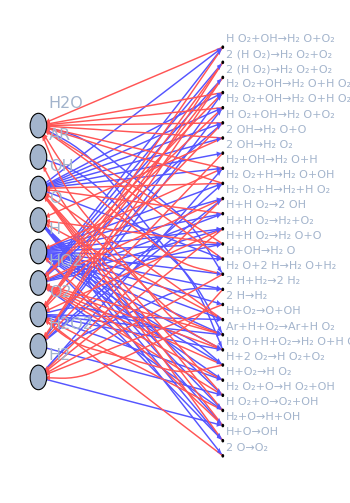

bipartite_reactions.pdf

```mathematica
filebase="data/combustionoh";
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],9]];
rates=Transpose[Partition[BinaryReadList[filebase<>"rates.npy","Real64"][[17;;-1]],28]];
rstois=Transpose[Partition[BinaryReadList[filebase<>"rstois.npy","Integer64"][[17;;-1]],28]];
pstois=Transpose[Partition[BinaryReadList[filebase<>"pstois.npy","Integer64"][[17;;-1]],28]];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
sptime[text_]:=First@FirstPosition[Accumulate[10^-12+concentrations[[First@FirstPosition[species,text]]]]/Total[10^-12+concentrations[[First@FirstPosition[species,text]]]],u_/;u>0.5]/Nt
sptimemin=Min[sptime/@species];
sptimemax=Max[sptime/@species];
spcol[text_]:=Blend[{Cyan,Orange},(sptime[text]-sptimemin)/(sptimemax-sptimemin)]
nreactions=Length[rstois];
Nt=Length[concentrations[[1]]];
tint=Interpolation[Transpose[{Range[Nt]/Nt,times}]];
reactants=Table[Extract[species,Position[rstois[[i]],u_/;u>0]],{i,1,nreactions}];
products=Table[Extract[species,Position[pstois[[i]],u_/;u>0]],{i,1,nreactions}];
r1=1.5;
r2=1;
colors={Lighter[Blue],Lighter[Red]};
weights=Mean/@rates;
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates/Nt;
wscale=Max[Abs[weights]];
ethrs=10^-64;
ethick=0.003;
shown=Flatten[Position[weights,u_/;Abs[u]>ethrs]];
edges=Table[If[weights[[i]]>0,Join[Table[reactants[[i,j]]->i,{j,1,Length[reactants[[i]]]}],Table[i->products[[i,j]],{j,1,Length[products[[i]]]}]],Join[Table[i->reactants[[i,j]],{j,1,Length[reactants[[i]]]}],Table[products[[i,j]]->i,{j,1,Length[products[[i]]]}]]],{i,1,nreactions}];
vertices=Union[species,DeleteDuplicates[Flatten[edges][[All,1]],Flatten[edges][[All,2]]]];
center=DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]];
centerspecies=SortBy[Complement[DeleteDuplicates[DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]]],Range[nreactions]],spcol[#]&];
centerreactions=Complement[center,centerspecies];
bottomspecies=SortBy[Complement[species,centerspecies],spcol[#]&];
bottomreactions=Complement[Range[nreactions],centerreactions];
rvcs=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]>ethrs]],GraphLayout->"SpiralEmbedding"]];
rvcs2=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],GraphLayout->"SpiralEmbedding"]];
{xmax,xmin,ymax,ymin}={Max[rvcs[[All,1]]],Min[rvcs[[All,1]]],Max[rvcs[[All,2]]],Min[rvcs[[All,2]]]};
{xmax2,xmin2,ymax2,ymin2}={Max[rvcs2[[All,1]]],Min[rvcs2[[All,1]]],Max[rvcs2[[All,2]]],Min[rvcs2[[All,2]]]};
trange=Quantile[Extract[weights2,Position[weights,u_/;Abs[u]>ethrs]],{0.25,0.75}];
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights[[edge[[1]]]],weights[[edge[[2]]]]];
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]];
vsize[text_]:=0.005+0.08*(Log[Max[Mean[concentrations[[First@FirstPosition[species,text]]]],10^-8]]/Log[10]+8)/8;
sizes={1.0,0.1,0.01,0.001,0.0001};
wsizes=Table[z/.First@Solve[(Log[Abs[z/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])==i*1.0/5,z],{i,5,1,-1}];

weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates;
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]]
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],Lighter[Red],Lighter[Blue]]
spforms={Subscript["H",2],"H","O",Subscript["O",2],"OH",DisplayForm[RowBox[{Subscript["H",2],"O"}]],DisplayForm[RowBox[{"H",Subscript["O",2]}]],DisplayForm[RowBox[{Subscript["H",2],Subscript["O",2]}]],"Ar"};
rnames=#[[1]]->#[[2]]&/@Transpose[{Total/@Table[Extract[rstois[[i]]*spforms,Position[rstois[[i]],u_/;u>0]],{i,1,nreactions}],Total/@Table[Extract[pstois[[i]]*spforms,Position[pstois[[i]],u_/;u>0]],{i,1,nreactions}]}];
plot=Graph[Flatten[{SortBy[species,sptime],SortBy[Range[Length[edges]],ecolor[edges[[#,1]]]&]}],Flatten[edges],GraphLayout->"BipartiteEmbedding",VertexLabels->(#->If[IntegerQ[#],rnames[[#]],Style[#,16]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{Hue[0.6,0.2,0.8],EdgeForm[Black]},{Opacity[1.0],Hue[0.6,0.2,0.8],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.05},{"Scaled",0.05}]]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]≤0,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[ecolor[#]],Thickness[ethick],Arrowheads[{{Abs[15*ethick],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->((If[#[[1,1]]>#[[2,1]],{Arrow[#,{0.0,0.075}]},{Arrow[#,{0.0,0.015}]}])&),AspectRatio->3/2,ImageSize->{350,Automatic}]
Export["bipartite_reactions.pdf",plot]
```

### fig3

```mathematica
filebase="data/nodimred/8"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=2*10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
edges=#[[1]]->#[[2]]&/@A2["NonzeroPositions"];
Export[filebase<>"edges.csv",Join[{{"Source","Target"}},{#[[1]],#[[2]]}&/@edges]];
AbsoluteTiming[g=Graph[#[[1]]->#[[2]]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[components=ConnectedComponents[g];]
Length[ConnectedComponents[g]]
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];Nt=Length[states];
AbsoluteTiming[componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];]
maxes=Max/@
Transpose[componentprob];
```

data/nodimred/8

{21717,9,0}

{0.560754,Null}

{0.020977,Null}

3023

{0.994877,Null}

```mathematica
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];Nt=Length[states];
AbsoluteTiming[componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];]
maxes=Max/@
Transpose[componentprob];
snodes=Flatten[Position[maxes,u_/;Abs[u]>10^-4]];
ptimes=(First/@Position[componentprob,#]&/@maxes[[snodes]])[[All,1]];
ptimes[[1]]=Nt;
scolors=cf/@ptimes;
edges=#[[1]]->#[[2]]&/@Import[filebase<>"edges.csv"][[2;;-1]];
AbsoluteTiming[edges=DeleteDuplicates[First@FirstPosition[components,#[[1]]]->First@FirstPosition[components,#[[2]]]&/@A2["NonzeroPositions"]];]
edges=DeleteCases[edges,u_/;u[[1]]==u[[2]]];
sizes=((Length/@components)/Total[Length/@components])^(1/2);
(Length/@components)[[#]]&/@snodes
Total[Length/@components]
N[Total[(Length/@components)[[#]]&/@snodes]/Total[Length/@components]]

AbsoluteTiming[p=LayeredGraphPlot[Graph[Range[Length[components]],edges],AspectRatio->1/2,ImageSize->dim^(1/2.)*20,EdgeStyle->Directive[Arrowheads[Small],Opacity[0.25]],VertexSize->Table[i->{"Scaled",0.15*sizes[[i]]},{i,1,Length[sizes]}],VertexStyle->Join[Table[snodes[[i]]->Directive[EdgeForm[Opacity[0.5]],scolors[[i]]],{i,1,Length[snodes]}],{Directive[EdgeForm[AbsoluteThickness[0.25]],RGBColor[{215/255,215/255,215/255}]]}],GraphStyle->{}];]
```

{1.1488,Null}

{346.334,Null}

{306,363,659,1118,1,1713,1}

21717

0.191601

{3126.6,Null}

```mathematica
vcs=p[[1,1,2,3;;-1]]/.Disk[{x_,y_},r_]:>{x,y}/.Style[p_,s_]:>p/.DynamicName[u_,v_]:>u;
svs=p[[1,1,2,3;;-1]]/.Disk[{x_,y_},r_]:>r/.Style[p_,s_]:>p/.DynamicName[u_,v_]:>u;
ssv=p[[1,1,2,3;;-1]]/.Disk[{x_,y_},r_]:>If[Abs[r]>0,Directive[EdgeForm[AbsoluteThickness[0.25]],RGBColor[{215/255,215/255,215/255}]],r]/.Style[p_,s_]:>s/.DynamicName[u_,v_]:>u;
ssv[[snodes]]=Table[Directive[EdgeForm[],scolors[[i]]],{i,1,Length[scolors]}]
If[filebase=="data/nodimred/3",vcs[[1,2]]=-10;vcs[[2,2]]=0;]
If[filebase=="data/nodimred/4",vcs[[3,2]]=10;vcs[[2,2]]=0;vcs[[1,2]]=-20;]
If[filebase=="data/nodimred/5",vcs[[1,2]]=-35;
vcs[[2,2]]=-10;]
If[filebase=="data/nodimred/6",vcs[[1,2]]=-60;
vcs[[2,2]]=-10;vcs[[5,1]]=-400;]
If[filebase=="data/nodimred/7",vcs[[1,2]]=-175;
vcs[[2,2]]=-100;
vcs[[3,2]]=0;
vcs[[5,1]]=-500;]
If[filebase=="data/nodimred/8",vcs[[1,2]]=-150;
vcs[[2,2]]=-50;
vcs[[5,1]]=-700;]
If[filebase=="data/nodimred/8",vcs[[1,2]]=-275;
vcs[[2,2]]=-175;vcs[[3,2]]=-75;vcs[[4,2]]=50;]
ed=p[[1,1,1]]/.DynamicName[u_]:>u/.Arrow[BezierCurve[{DynamicLocation[s1_,Automatic,Center],l__,DynamicLocation[s2_,Automatic,Center]}]]:>Arrow[BezierCurve[Join[{vcs[[ToExpression[StringSplit[s1,"$"][[2]]]]]},{l},{vcs[[ToExpression[StringSplit[s2,"$"][[2]]]]]}]],{0,svs[[ToExpression[StringSplit[s2,"$"][[2]]]]]}]/.Arrow[{DynamicLocation[s1_,Automatic,Center],DynamicLocation[s2_,Automatic,Center]}]:>Arrow[{vcs[[ToExpression[StringSplit[s1,"$"][[2]]]]],vcs[[ToExpression[StringSplit[s2,"$"][[2]]]]]},{0,svs[[ToExpression[StringSplit[s2,"$"][[2]]]]]}]/.DynamicName[u_,v_]:>u;
vd=Join[{Directive[Hue[0.6, 0.2, 0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]],Directive[EdgeForm[AbsoluteThickness[0.25]],RGBColor[{215/255,215/255,215/255}]]},Flatten[Table[{ssv[[i]],Disk[vcs[[i]],svs[[i]]]},{i,1,Length[vcs]}]]];
plot=Graphics[{ed,vd},ImageSize->dim^(1/2.)*20];
Rasterize[plot]
Export[filebase<>"scaledconnected.pdf",plot]
plot2=Graphics[{ed,vd},ImageSize->1000];
Export[filebase<>"connected.pdf",plot2]
```

{Directive[EdgeForm[],RGBColor[0., 0.6666666666666666, 0.]],Directive[EdgeForm[],RGBColor[0.4719471947194719, 0.40264026402640263, 0.8613861386138615]],Directive[EdgeForm[],RGBColor[0.4983498349834983, 0.4158415841584158, 0.834983498349835]],Directive[EdgeForm[],RGBColor[0.5115511551155115, 0.42244224422442245, 0.8217821782178218]],Directive[EdgeForm[],RGBColor[0.5775577557755776, 0.4554455445544554, 0.7557755775577558]],Directive[EdgeForm[],RGBColor[0.6303630363036303, 0.4818481848184818, 0.702970297029703]],Directive[EdgeForm[],RGBColor[0.9867986798679867, 0.6600660066006601, 0.3465346534653465]]}

-Graphics-

data/nodimred/8scaledconnected.pdf

data/nodimred/8connected.pdf

### fig4

{data/dimred4/3,data/dimred4/4,data/dimred4/5,data/dimred4/6,data/dimred4/7,data/dimred4/8,data/dimred4/9,data/dimred4/10,data/dimred4/11,data/dimred4/12,data/dimred4/13,data/dimred4/14,data/dimred4/15}

{data/nodimred/3,data/nodimred/4,data/nodimred/5,data/nodimred/6,data/nodimred/7,data/nodimred/8,data/nodimred/9,data/nodimred/10}

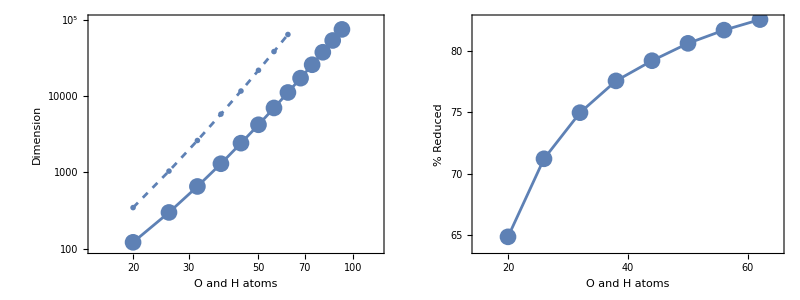

fig2.pdf

```mathematica
initials={};
filebases=Table["data/dimred4/"<>ToString[i],{i,3,15,1}]
dims={};
Do[
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];AppendTo[dims,dim];,{filebase,filebases}]
filebases=Table["data/nodimred/"<>ToString[i],{i,3,10,1}]
dims2={};
Do[
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];AppendTo[dims2,dim];,{filebase,filebases}]
p=Grid[{{Show[ListLogLogPlot[Transpose[{2+(0+2+4)*(Range[Length[dims]]+2),dims}],AspectRatio->1,Joined->True,Axes->False,Frame->True,FrameLabel->{"O and H atoms","Dimension"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[AbsoluteThickness[2]],ImageSize->300,ImagePadding->{{75,15},{75,15}},PlotRange->{{15,120},{100,10^5}},FrameTicks->{{Table[{10^n,With[{n=n},HoldForm[10^n]]},{n,2,5}],Table[{10^n,""},{n,2,5}]},{Table[{10^n,With[{n=PaddedForm[n,{3,2}]},HoldForm[10^n]]},{n,0.25,2,0.25}],Table[{2^n,""},{n,6,10}]}}],ListLogLogPlot[Transpose[{2+(0+2+4)*(Range[Length[dims]]+2),dims}],Joined->False,PlotStyle->Directive[PointSize[0.04]]],ListLogLogPlot[Transpose[{2+(0+2+4)*(Range[Length[dims2]]+2),dims2}],Joined->True,PlotStyle->Directive[AbsoluteThickness[2],Dashed]],ListLogLogPlot[Transpose[{2+(0+2+4)*(Range[Length[dims2]]+2),dims2}],Joined->False,PlotStyle->Directive[PointSize[0.02]],PlotMarkers->{Graphics[{Circle[],White,Disk[]}],0.05}]],Show[ListPlot[Transpose[{2+(0+2+4)*(Range[Length[dims2]]+2),100*(1-dims[[1;;8]]/dims2)}],AspectRatio->1,Joined->True,Axes->False,Frame->True,FrameLabel->{"O and H atoms","% Reduced"},LabelStyle->Directive[Black,16],PlotRange->{{15,65},Automatic},ImageSize->300,ImagePadding->{{75,15},{75,15}},FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,65,85,5}],Table[{i,""},{i,65,85,5}]},{Table[{i,i},{i,20,75,10}],Table[{i,""},{i,20,75,10}]}}],ListPlot[Transpose[{2+(0+2+4)*(Range[Length[dims2]]+2),100*(1-dims[[1;;8]]/dims2)}],Joined->False,PlotStyle->Directive[PointSize[0.04]]]]}}]
Export["fig2.pdf",p]
```

```mathematica
Transpose[{2+(0+2+4)*(Range[Length[dims]]+2),dims}]
Transpose[{2+(0+2+4)*(Range[Length[dims2]]+2),dims2}]
```

{{20,122},{26,300},{32,656},{38,1301},{44,2418},{50,4207},{56,6982},{62,11129},{68,17131},{74,25664},{80,37375},{86,53303},{92,74421}}

{{20,347},{26,1042},{32,2621},{38,5799},{44,11631},{50,21717},{56,38164},{62,63835}}

-5.90986+3.57254 x

-7.0327+4.29728 x

0.00271256 n^3.57254

0.000882542 n^4.29728

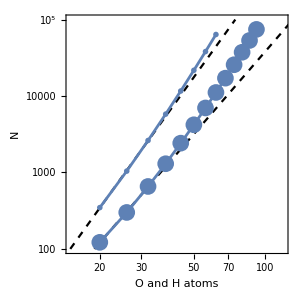

fig4a.pdf

```mathematica
f1[x_]=Fit[Log[Transpose[{2+(0+2+4)*(Range[Length[dims]]+2),dims}]][[1;;3]],{1,x},x]
f2[x_]=Fit[Log[Transpose[{2+(0+2+4)*(Range[Length[dims2]]+2),dims2}]][[1;;3]],{1,x},x]
Exp[f1[Log[n]]]
Exp[f2[Log[n]]]
p=Show[LogLogPlot[{Exp[f1[Log[n]]],Exp[f2[Log[n]]]},{n,1,200},PlotStyle->Directive[Black,Dashed],AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"O and H atoms","N"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,ImagePadding->{{75,15},{75,15}},PlotRange->{{15,120},{100,10^5}},FrameTicks->{{Table[{10^n,With[{n=n},HoldForm[10^n]]},{n,2,5}],Table[{10^n,""},{n,2,5}]},{Table[{10^n,With[{n=PaddedForm[n,{3,2}]},HoldForm[10^n]]},{n,0.25,2,0.25}],Table[{2^n,""},{n,6,10}]}}],ListLogLogPlot[Transpose[{2+(0+2+4)*(Range[Length[dims]]+2),dims}],Joined->True,PlotStyle->Directive[AbsoluteThickness[2]]],ListLogLogPlot[Transpose[{2+(0+2+4)*(Range[Length[dims]]+2),dims}],Joined->False,PlotStyle->Directive[PointSize[0.04]]],ListLogLogPlot[Transpose[{2+(0+2+4)*(Range[Length[dims2]]+2),dims2}],Joined->True,PlotStyle->Directive[AbsoluteThickness[2]]],ListLogLogPlot[Transpose[{2+(0+2+4)*(Range[Length[dims2]]+2),dims2}],Joined->False,PlotStyle->Directive[PointSize[0.02]],PlotMarkers->{Graphics[{Circle[],White,Disk[]}],0.05}]]
Export["fig4a.pdf",p]
```

### fig5

```mathematica
filebase="data/dimred4/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
ind=First@FirstPosition[multiindices,dat[[2]]];
```

{11129,9,124.557}

```mathematica
evals=BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]];
evecs=Partition[BinaryReadList[filebase<>"eigenvectors.npy","Complex128"][[9;;-1]],dim];
```

```mathematica
evals[[-1]]
order=Reverse[Ordering[Abs[evecs[[-1]]]]];
Abs[evecs[[-1]][[order[[1;;24]]]]/Total[evecs[[-1]]]]
Total[evecs[[-1]][[order[[1;;24]]]]/Total[evecs[[-1]]]]
multiindices[[order[[1;;24]]]]
Abs[Total[multiindices[[order[[1;;24]]]]*(evecs[[-1]][[order[[1;;24]]]]/Total[evecs[[-1]]])]]
Abs[Total[multiindices[[order[[1;;24]]]]*(evecs[[-1]][[order[[1;;24]]]]/Total[evecs[[-1]]])]]*{"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"}
Export["topmultiindices.csv",multiindices[[order[[1;;24]]]]]
Export["topprobability.csv",Abs[evecs[[-1]][[order[[1;;24]]]]/Total[evecs[[-1]]]]]
Export["expectedspecies.csv",{{"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"},Abs[Total[multiindices[[order[[1;;24]]]]*(evecs[[-1]][[order[[1;;24]]]]/Total[evecs[[-1]]])]]}]
```

-3.39113×10^-7+0. ⅈ

{0.585636,0.159483,0.0973159,0.0523631,0.044289,0.0395957,0.0102543,0.00240438,0.00179593,0.00133066,0.00097328,0.000874345,0.000799636,0.000676548,0.000579433,0.000271753,0.00027072,0.00021572,0.000195964,0.00019358,0.000152716,0.000107619,0.000099512,0.0000703835}

0.999948+0. ⅈ

{{0,0,0,0,1,20,0,0,200},{2,0,0,1,1,18,0,0,200},{1,1,0,1,0,19,0,0,200},{1,0,0,0,3,18,0,0,200},{0,1,0,0,2,19,0,0,200},{1,0,1,0,1,19,0,0,200},{0,1,1,0,0,20,0,0,200},{2,1,0,1,2,17,0,0,200},{1,2,0,1,1,18,0,0,200},{3,1,0,2,0,17,0,0,200},{2,1,1,1,0,18,0,0,200},{3,0,1,1,1,17,0,0,200},{4,0,0,2,1,16,0,0,200},{3,0,0,1,3,16,0,0,200},{1,1,1,0,2,18,0,0,200},{1,1,0,0,4,17,0,0,200},{2,0,1,0,3,17,0,0,200},{0,3,0,1,0,19,0,0,200},{0,2,0,0,3,18,0,0,200},{0,2,1,0,1,19,0,0,200},{2,0,2,0,1,18,0,0,200},{1,0,0,0,0,19,1,0,200},{1,1,2,0,0,19,0,0,200},{2,0,0,0,5,16,0,0,200}}

{0.530681,0.162536,0.0532457,0.267999,1.04503,19.3644,0.000107619,0.,199.99}

{0.530681 H2,0.162536 H,0.0532457 O,0.267999 O2,1.04503 OH,19.3644 H2O,0.000107619 HO2,0.,199.99 AR}

topmultiindices.csv

topprobability.csv

expectedspecies.csv

```mathematica
Export["order.csv",order[[1;;24]]]
```

order.csv

```mathematica
evals=BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]];
evecs=Partition[BinaryReadList[filebase<>"eigenvectors.npy","Complex128"][[9;;-1]],dim];
α=BinaryReadList[filebase<>"alpha.npy","Complex128"][[9;;-1]];
dim2=150;
order=dim-1000+Reverse[Ordering[Abs[α[[-1000;;-1]]]]];
AbsoluteTiming[evecs3=evecs[[order[[1;;dim2]]]];]
AbsoluteTiming[angles=Re[(evecs3.ConjugateTranspose[evecs3])/Outer[Times,Norm/@evecs3,Norm/@evecs3]];]
```

{0.000038,Null}

{0.655015,Null}

```mathematica
dim2=150;
h1=Histogram[{Log[Re[-1/evals[[1;;-2]]]]/Log[10],Log[Re[-1/evals[[order[[1;;dim2]]]]]]/Log[10]},{-9,-2,(-2-(-9))/50},"Count",PlotRange->{{-9,-1.5},All},ChartStyle->{Directive[Opacity[0.5],Lighter[Gray]],Directive[Blue,Opacity[0.5]]},AspectRatio->1/7,Axes->{True,False},Ticks->None,ImagePadding->None,PlotRangePadding->None,ImageSize->(350-95-25),ChartLayout->"Overlapped"];
h2=Rotate[Histogram[{-Log[Abs[α]]/Log[10],-Log[Abs[α[[order[[1;;dim2]]]]]]/Log[10]},{-6,15,(6-(-15))/50},"Count",PlotRange->{{-6,15},All},ChartStyle->{Directive[Opacity[0.5],Lighter[Gray]],Directive[Blue,Opacity[0.5]]},AspectRatio->1/7,Axes->{True,False},Ticks->None,ImagePadding->None,PlotRangePadding->None,ImageSize->(350-95-25),ChartLayout->"Overlapped"],-Pi/2];


p=rasterizeBackground[ListLogLogPlot[{Transpose[{-1/evals,Abs[α]}][[1;;-2]],Transpose[{-1/evals[[order[[1;;dim2]]]],Abs[α][[order[[1;;dim2]]]]}][[2;;-1]]},PlotRange->{{10^-9,10^-1.5},{10^-15,10^6}},FrameTicks->{{Table[{10^i,With[{i=ToString[i]},HoldForm[10^i]]},{i,-15,5,5}],Table[{10^i,""},{i,-15,5,5}]},{Table[{10^i,With[{i=ToString[i]},HoldForm[10^i]]},{i,-8,-2,2}],Table[{10^i,""},{i,-8,-2,2}]}},Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Subscript[τ,n],"(sec)"}]],Abs[Subscript["α",n]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->{450,450},ImagePadding->{{95,125},{95,125}},PlotStyle->{Directive[PointSize[0.02],Opacity[0.5],Lighter[Gray]],Directive[PointSize[0.02],Opacity[0.5],Blue]},Epilog->{Inset[h1,Scaled[{0.5,1.1}]],Inset[h2,Scaled[{1.1,0.5}]]},PlotRangeClipping->False]]

Export["fig3a.pdf",p]
```

-Graphics-

fig3a.pdf

```mathematica
evals[[-1]]=0;
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
times=Import[filebase<>"times.npy","Real64"][[17;;-1]];
index=First@FirstPosition[multiindices,dat[[2]]]
pinv=PseudoInverse[evecs[[order[[1;;dim2]]]]];
α2=SparseArray[{index->1},dim].pinv;
Norm[Re[α2.evecs[[order[[1;;dim2]]]]]-SparseArray[{index->1},dim],Infinity]
Monitor[states2=Table[pos=Flatten[Position[evals[[order[[1;;dim2]]]],u_/;Abs[u*t]<100]];Re[(α2[[pos]]*Exp[t*evals[[order[[pos]]]]]).evecs[[order[[pos]]]]],{t,times}];,t]
Norm[Flatten[(states-states2)],Infinity]
```

1

0.000119488

0.000271044

```mathematica
pinv2=PseudoInverse[evecs[[-1000;;-1]]];
α3=SparseArray[{index->1},dim].pinv2;
evecs3=evecs[[-1000;;-1]];
evals3=evals[[-1000;;-1]];
Norm[Re[α3.evecs3]-SparseArray[{index->1},dim],1]
Monitor[states3=Table[pos=Flatten[Position[evals3,u_/;Abs[u*t]<100]];Re[(α3[[pos]]*Exp[t*evals3[[pos]]]).evecs3[[pos]]],{t,times}];,t]
Norm[Flatten[(states-states3)],Infinity]
```

3.62413×10^-6

1.49579×10^-6

```mathematica
p=Legended[rasterizeBackground[MatrixPlot[Re[ArcCos[Abs[angles[[1;;dim2,1;;dim2]]]]],ColorFunctionScaling->False,ColorFunction->(Blend[{Blue,Lighter[Yellow]},#/(Pi/2)]&),ClippingStyle->None,PlotRange->{{1,1+dim2},{1,1+dim2},{0,Pi/2}},PlotRangePadding->None,FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16],FrameLabel->{{None,j},{i,None}},FrameTicks->{{{1,30,60,90,120,150},{{0,""},{30,""},{60,""},{90,""},{120,""},{150,""}}},{{{0,""},{30,""},{60,""},{90,""},{120,""},{150,""}},{1,30,60,90,120,150}}},ImageSize->{450,450},ImagePadding->{{95,125},{95,125}},ColorFunction->"TemperatureMap",PlotRange->{0,1},MaxPlotPoints->Infinity]],MatrixPlot[Table[i,{i,0,100},{j,0,100}],ColorFunction->(Blend[{Blue,Lighter[Yellow]},#/(100)]&),ColorFunctionScaling->False,AspectRatio->10,ImageSize->{Automatic,200},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{{None,Subscript[θ,ij]},{None,None}},FrameTicks->{{None,{{1,0},{26,DisplayForm[RowBox[{Pi,"/",8}]]},{51,DisplayForm[RowBox[{Pi,"/",4}]]},{76,DisplayForm[RowBox[{3Pi,"/",8}]]},{101,DisplayForm[RowBox[{Pi,"/",2}]]}}},{None,None}},DataReversed->True,LabelStyle->Directive[16,Black]]]
Export["fig3c.pdf",p]
```

-Graphics-

fig3c.pdf

```mathematica
Length[BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]]]
```

4000

```mathematica
(* Note: dimred4 currently consists of all eigenvalues in the projection. Should we restrict to the 150 blue ones, as above? *)
```

{11129,9,124.557}

{11129,9,124.557}

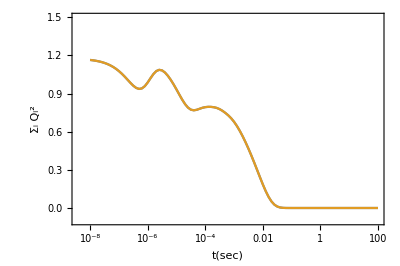

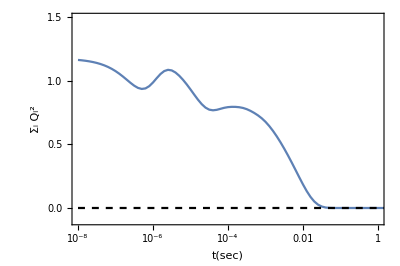

fig3d.pdf

```mathematica
filebase="data/dimred4/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=Import[filebase<>"times.npy","Real64"][[17;;-1]];
evals=BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]];
evecs=Partition[BinaryReadList[filebase<>"eigenvectors.npy","Complex128"][[9;;-1]],dim];
evals[[-1]]=0;
steady=evecs[[-1]]/Total[evecs[[-1]]];
l1=Transpose[{times,Norm[Re[#-steady]]&/@states}];
filebase="data/dimred4/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
times=Import[filebase<>"times.npy","Real64"][[17;;-1]];
steady=Re[evecs[[-1]]/Total[evecs[[-1]]]];
l2=Transpose[{times,Norm[Re[#-steady]]&/@states}];
ListLogLinearPlot[{l1,l2},Joined->True,Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{t,"(sec)"}]],DisplayForm[RowBox[{Subscript["Σ",i],Subscript[Q,i]^2}]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[16,AbsoluteThickness[2]],AspectRatio->2/3,PlotRange->{-0.1,1.5}]
p=ListLogLinearPlot[{l1,{{10^-8,0},{10^2,0}}},Joined->True,Axes->False,Frame->True,PlotStyle->{Automatic,Directive[Black,Dashed]},FrameLabel->{DisplayForm[RowBox[{t,"(sec)"}]],DisplayForm[RowBox[{Subscript["Σ",i],Subscript[Q,i]^2}]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[16,AbsoluteThickness[2]],AspectRatio->2/3,PlotRange->{{10^-8,10^0},{-0.1,1.5}},FrameTicks->{{{{0.,PaddedForm[0.,{2,1}]},{0.5,PaddedForm[0.5,{2,1}]},{1.,PaddedForm[1.,{2,1}]},{1.5,PaddedForm[1.5,{2,1}]}},{{0,""},{0.5,""},{1,""},{1.5,""}}},{{{10^-8,10^"-8"},{10^-6,10^"-6"},{10^-4,10^"-4"},{10^-2,10^"-2"},{10^0,10^"0"}},{{10^-8,""},{10^-6,""},{10^-4,""},{10^-2,""},{10^0,""}}}}]
Export["fig3d.pdf",p]
```

```mathematica
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
concentrations=Table[Transpose[{times,(Total/@(states.concentrationnorms[[i]]))}],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
temps=Transpose[{times,(Total/@(states.temperaturenorm))}];
tig=First@FirstPosition[Differences[temps[[All,2]]],Max[Differences[temps[[All,2]]]]]
evals=BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]];
evecs=Partition[BinaryReadList[filebase<>"eigenvectors.npy","Complex128"][[9;;-1]],dim];
evals[[-1]]=0;
steady=evecs[[-1]]/Total[evecs[[-1]]];
l1=Transpose[{times,Norm[Re[#-steady]]&/@states}];
```

40

```mathematica
t3=Exp[x]/.FindMaximum[Interpolation[temps]'[Exp[x]],{x,-10,-12,-8}][[2]]
t1=Exp[x]/.FindMaximum[Interpolation[Log[temps]]'[x],{x,-10,-15,-8}][[2]]
t2=Exp[x]/.FindMaximum[Interpolation[Log[temps]]'[x],{x,-5,-8,-2}][[2]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0000489097

0.0000724076

0.00653857

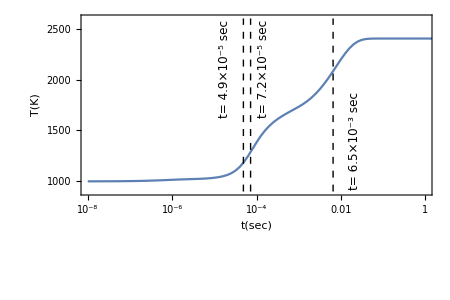

temperatures.pdf

```mathematica
p=ListLogLinearPlot[{{#[[1]],#[[2]]}&/@temps,{{t1,900},{t1,2600}},{{t3,900},{t3,2600}},{{t2,900},{t2,2600}}},Joined->True,Axes->False,Frame->True,PlotRange->{{10^-8,10^0},{900,2600}},ImagePadding->{{75,75},{65,15}},ImageSize->450,FrameLabel->{{"T(K)",None},{DisplayForm[RowBox[{t,"(sec)"}]],None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[16,AbsoluteThickness[2]],AspectRatio->2/3,PlotStyle->{ColorData[97,"ColorList"][[1]],Directive[Dashed,AbsoluteThickness[1],Black],Directive[Dashed,AbsoluteThickness[1],Black],Directive[Dashed,AbsoluteThickness[1],Black]},PlotLabels->{Placed[Style[Subscript["H",2],ColorData[97,"ColorList"][[2]]],{10^-7,0.9}],Placed[Style[Subscript["O",2],ColorData[97,"ColorList"][[3]]],{10^-7,0.4}],Placed[Style[DisplayForm[RowBox[{Subscript["H",2],"O"}]],ColorData[97,"ColorList"][[4]]],{10^-1,0.9}]},FrameTicks->{{{1000,1500,2000,2500},{{1000,""},{1500,""},{2000,""},{2500,""}}},{{{10^-8,10^"-8"},{10^-6,10^"-6"},{10^-4,10^"-4"},{10^-2,10^"-2"},{10^0,10^"0"}},{{10^-8,""},{10^-6,""},{10^-4,""},{10^-2,""},{10^0,""}}}},Epilog->{Inset[Rotate[Style[DisplayForm[RowBox[{"t=",PaddedForm[t1*10^5,{2,1}],"×",10^-"5","sec"}]],12],Pi/2],Scaled[{0.52,0.7}]],Inset[Rotate[Style[DisplayForm[RowBox[{"t=",PaddedForm[t3*10^5,{2,1}],"×",10^-"5","sec"}]],12],Pi/2],Scaled[{0.41,0.7}]],Inset[Rotate[Style[DisplayForm[RowBox[{"t=",PaddedForm[t2*10^3,{2,1}],"×",10^-"3","sec"}]],12],Pi/2],Scaled[{0.78,0.3}]]}]
Export["temperatures.pdf",p]
```

```mathematica
Export["temps.csv",temps]
```

temps.csv

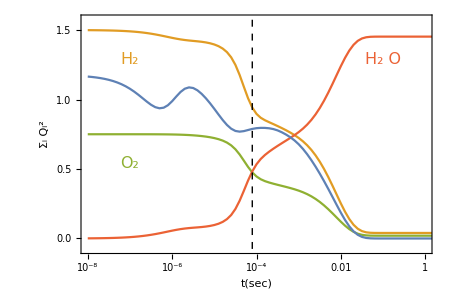

fig3d.pdf

```mathematica
p=ListLogLinearPlot[{{#[[1]],#[[2]]/20}&/@concentrations[[1]],{#[[1]],#[[2]]/20}&/@concentrations[[4]],{#[[1]],#[[2]]/20}&/@concentrations[[6]],{#[[1]],#[[2]]/1.5}&/@l1,{{times[[tig]],-0.050},{times[[tig]],1.05}}},Joined->True,Axes->False,Frame->True,PlotRange->{{10^-8,10^0},{-0.050,1.05}},ImagePadding->{{75,75},{65,15}},ImageSize->450,FrameLabel->{{Style[DisplayForm[RowBox[{Subscript["Σ",i],Subscript[Q,i]^2}]],ColorData[97,"ColorList"][[1]]],Subscript[n,i]},{DisplayForm[RowBox[{t,"(sec)"}]],None}},LabelStyle->Directive[16,Black],PlotStyle->{ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[1]],Directive[Dashed,AbsoluteThickness[1],Black]},FrameStyle->Directive[16,AbsoluteThickness[2]],AspectRatio->2/3,PlotLabels->{Placed[Style[Subscript["H",2],ColorData[97,"ColorList"][[2]]],{10^-7,0.9}],Placed[Style[Subscript["O",2],ColorData[97,"ColorList"][[3]]],{10^-7,0.4}],Placed[Style[DisplayForm[RowBox[{Subscript["H",2],"O"}]],ColorData[97,"ColorList"][[4]]],{10^-1,0.9}]},FrameTicks->{{{{0.,PaddedForm[0.,{2,1}]},{1/3,PaddedForm[0.5,{2,1}]},{2/3,PaddedForm[1.0,{2,1}]},{1,PaddedForm[1.5,{2,1}]}},{{0.,0},{0.5,10},{1.,20}}},{{{10^-8,10^"-8"},{10^-6,10^"-6"},{10^-4,10^"-4"},{10^-2,10^"-2"},{10^0,10^"0"}},{{10^-8,""},{10^-6,""},{10^-4,""},{10^-2,""},{10^0,""}}}}]
Export["fig3d.pdf",p]
```

7.9×10^-5

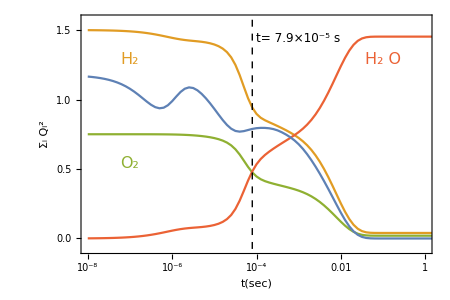

fig3d.pdf

```mathematica
DisplayForm[RowBox[{PaddedForm[times[[tig]]*10^5,{2,1}],"×",10^-"5"}]]
p=ListLogLinearPlot[{{#[[1]],#[[2]]/20}&/@concentrations[[1]],{#[[1]],#[[2]]/20}&/@concentrations[[4]],{#[[1]],#[[2]]/20}&/@concentrations[[6]],{#[[1]],#[[2]]/1.5}&/@l1,{{times[[tig]],-0.050},{times[[tig]],1.05}}},Joined->True,Axes->False,Frame->True,PlotRange->{{10^-8,10^0},{-0.050,1.05}},ImagePadding->{{75,75},{65,15}},ImageSize->450,FrameLabel->{{Style[DisplayForm[RowBox[{Subscript["Σ",i],Subscript[Q,i]^2}]],ColorData[97,"ColorList"][[1]]],Subscript[n,i]},{DisplayForm[RowBox[{t,"(sec)"}]],None}},LabelStyle->Directive[16,Black],PlotStyle->{ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[1]],Directive[Dashed,AbsoluteThickness[1],Black]},FrameStyle->Directive[16,AbsoluteThickness[2]],AspectRatio->2/3,PlotLabels->{Placed[Style[Subscript["H",2],ColorData[97,"ColorList"][[2]]],{10^-7,0.9}],Placed[Style[Subscript["O",2],ColorData[97,"ColorList"][[3]]],{10^-7,0.4}],Placed[Style[DisplayForm[RowBox[{Subscript["H",2],"O"}]],ColorData[97,"ColorList"][[4]]],{10^-1,0.9}]},FrameTicks->{{{{0.,PaddedForm[0.,{2,1}]},{1/3,PaddedForm[0.5,{2,1}]},{2/3,PaddedForm[1.0,{2,1}]},{1,PaddedForm[1.5,{2,1}]}},{{0.,0},{0.5,10},{1.,20}}},{{{10^-8,10^"-8"},{10^-6,10^"-6"},{10^-4,10^"-4"},{10^-2,10^"-2"},{10^0,10^"0"}},{{10^-8,""},{10^-6,""},{10^-4,""},{10^-2,""},{10^0,""}}}},Epilog->{Inset[Style[DisplayForm[RowBox[{"t=",PaddedForm[times[[tig]]*10^5,{2,1}],"×",10^-"5","s"}]],12],Scaled[{0.62,0.9}]]}]
Export["fig3d.pdf",p]
```

### fig6

```mathematica
filebase="data/dimred4/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],Table[{rows[[i]]+1,rows[[i]]+1}->-data[[i]],{i,1,Length[data]}]],{dim,dim}];
```

```mathematica
AbsoluteTiming[{rvals,rvecs}=Eigensystem[((A+Transpose[A])/2)];]
file=OpenWrite["10rvals.dat","BinaryFormat"->True]
BinaryWrite[file,rvals,"Complex128"]
Close[file]
file=OpenWrite["10rvecs.dat","BinaryFormat"->True]
BinaryWrite[file,Flatten[rvecs],"Complex128"]
Close[file]
```

Eigensystem::arh: Because finding 11129 out of the 11129 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

{167.984,Null}

OutputStream[…]

OutputStream[…]

10rvals.dat

OutputStream[…]

OutputStream[…]

10rvecs.dat

```mathematica
AbsoluteTiming[rvals=BinaryReadList["10rvals.dat","Complex128"];]
AbsoluteTiming[rvecs=Partition[BinaryReadList["10rvecs.dat","Complex128"],dim];]
AbsoluteTiming[evals=BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]];]
AbsoluteTiming[evecs=Partition[BinaryReadList[filebase<>"eigenvectors.npy","Complex128"][[9;;-1]],dim];]
AbsoluteTiming[pinv=Partition[BinaryReadList[filebase<>"pinv.npy","Complex128"][[9;;-1]],dim];]
optimum=Reverse[Ordering[rvals]][[1]];
ic=rvecs[[optimum]]/Total[rvecs[[optimum]]];
steady=evecs[[-1]]/Total[evecs[[-1]]];
rvals[[optimum]]
AbsoluteTiming[α=pinv.ic;]
file=OpenWrite["10alpha1.dat","BinaryFormat"->True]
BinaryWrite[file,Flatten[{Re[#],Im[#]}&/@α],"Real64"]
Close[file]
index=First@FirstPosition[multiindices,dat[[2]]];
AbsoluteTiming[α=pinv.SparseArray[{index,0},{dim}];]
file=OpenWrite["10alpha2.dat","BinaryFormat"->True]
BinaryWrite[file,Flatten[{Re[#],Im[#]}&/@α],"Real64"]
Close[file]
```

{0.011634,Null}

{15.1324,Null}

{0.012043,Null}

{55.8783,Null}

{68.8526,Null}

5.56848×10^7+0. ⅈ

```mathematica
AbsoluteTiming[rvals=BinaryReadList["10rvals.dat","Complex128"];]
AbsoluteTiming[rvecs=Partition[BinaryReadList["10rvecs.dat","Complex128"],dim];]
AbsoluteTiming[evals=BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]];]
AbsoluteTiming[evecs=Partition[BinaryReadList[filebase<>"eigenvectors.npy","Complex128"][[9;;-1]],dim];]
AbsoluteTiming[α1=BinaryReadList["10alpha1.dat","Complex128"];]
AbsoluteTiming[α2=BinaryReadList["10alpha2.dat","Complex128"];]
optimum=Reverse[Ordering[rvals]][[1]];

evals[[-1]]=0;
t0=1/rvals[[optimum]]/100;
t1=10^2;
Nt=250;
times=Table[t0*(t1/t0)^(i/(Nt-1)),{i,0,(Nt-1)}];
AbsoluteTiming[Monitor[states=Table[pos=Flatten[Position[evals*t,u_/;Abs[u]<100]];(Exp[evals[[pos]]*t]*α1[[pos]]).evecs[[pos]],{t,times}];,t]]
AbsoluteTiming[Monitor[states2=Table[pos=Flatten[Position[evals*t,u_/;Abs[u]<100]];(Exp[evals[[pos]]*t]*α2[[pos]]).evecs[[pos]],{t,times}];,t]]
```

{222.425,Null}

{243.877,Null}

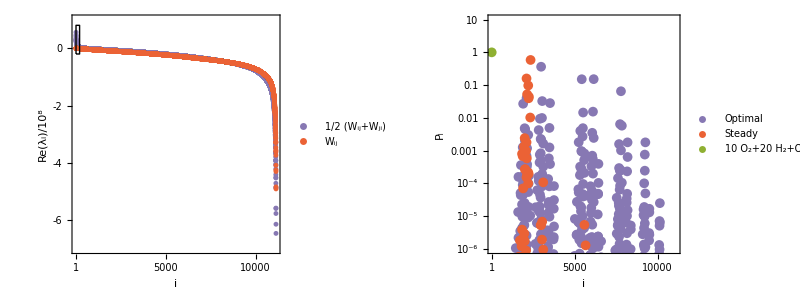
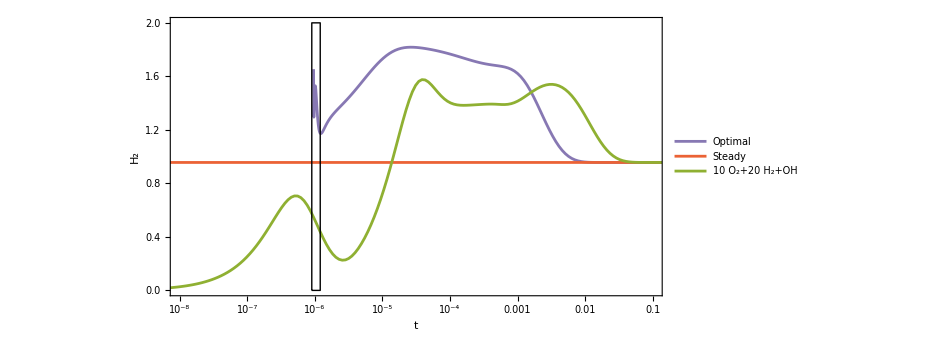

figs/entropy.pdf

```mathematica
index=First@FirstPosition[multiindices,dat[[2]]];
inset0=ListPlot[{Reverse[Sort[Re[rvals]]],Reverse[Re[evals]]}[[All,1;;200]]/10^8,PlotStyle->{Directive[ColorData[97,"ColorList"][[5]],PointSize[0.02]],Directive[ColorData[97,"ColorList"][[4]],PointSize[0.02]]},Axes->False,Frame->True,FrameLabel->None,PlotRange->{-0.2,0.8},FrameTicks->{{{0,0.3, 0.6},{{0,""},{0.3,""},{0.6,""}}},{{{1,1},{100,100},{200,200}},{{1,""},{100,""},{200,""}}}},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImagePadding->{{65,10},{65,10}},ImageSize->200];
p1=ListPlot[{Reverse[Sort[Re[rvals]]],Reverse[Re[evals]]}/10^8,PlotStyle->{Directive[ColorData[97,"ColorList"][[5]],PointSize[0.01]],Directive[ColorData[97,"ColorList"][[4]],PointSize[0.01]]},Axes->False,Frame->True,FrameLabel->{i,DisplayForm[RowBox[{Re[Subscript[λ,i]],"/",HoldForm[10^8]}]]},PlotRange->{-7,1},FrameTicks->{{{-8,-6,-4,-2,0},{{-8,""},{-6,""},{-4,""},{-2,""},{0,""}}},{{{1,1},{5000,5000},{10000,10000}},{{1,""},{5000,""},{10000,""}}}},PlotLegends->Placed[{1/2*(Subscript[W,ij]+Subscript[W,ji]),Subscript[W,ij]},{0.5,0.85}],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{65,10},{65,10}},Epilog->{Line[{{1,-0.2},{200,-0.2},{200,0.8},{1,0.8},{1,-0.2}}],Inset[inset0,Scaled[{0.4,0.3}]]}];
p2=ListLogPlot[Re[{rvecs[[optimum]]/Total[rvecs[[optimum]]],evecs[[-1]]/Total[evecs[[-1]]],SparseArray[index->1,{dim}]}],PlotRange->{10^-6,10^1},PlotStyle->{Directive[ColorData[97,"ColorList"][[5]],PointSize[0.02]],Directive[ColorData[97,"ColorList"][[4]],PointSize[0.02]],Directive[ColorData[97,"ColorList"][[3]],PointSize[0.02]]},Axes->False,Frame->True,FrameLabel->{i,Subscript[P,i]},FrameTicks->{{{{10^-6,HoldForm[10^"-6"]},{10^-4,HoldForm[10^"-4"]},{10^-2,HoldForm[10^"-2"]},{10^0,HoldForm[10^"0"]}},{{10^-6,""},{10^-4,""},{10^-2,""},{10^0,""}}},{{{1,1},{5000,5000},{10000,10000}},{{1,""},{5000,""},{10000,""}}}},PlotLegends->Placed[{"Optimal","Steady",DisplayForm[RowBox[{"10",Subscript["O", 2],"+20",Subscript["H", 2],"+OH"}]]},{0.75,0.75}],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{65,10},{65,10}}];
tmin=times[[1+First@FirstPosition[#,Min[#]]&@(Differences[-Log[Norm[#]]&/@states2]/Differences[times])]];

t2=9*10^-7;
t3=12*10^-7;
inset=ListPlot[{Cases[Transpose[{times+tmin,-Log[Norm[#]^2]&/@states}],u_/;u[[1]]>5*10^-7&&u[[1]]<2*10^-6],{{5*10^-7,-Log[Norm[evecs[[-1]]/Total[evecs[[-1]]]]^2]},{2*10^-6,-Log[Norm[evecs[[-1]]/Total[evecs[[-1]]]]^2]}},Cases[Transpose[{times,-Log[Norm[#]^2]&/@states2}],u_/;u[[1]]>5*10^-7&&u[[1]]<2*10^-6]},PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[5]],PointSize[0.01]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[4]],PointSize[0.01]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]],PointSize[0.01]]},Axes->False,Frame->True,FrameLabel->None,LabelStyle->Directive[Black,16],FrameStyle->Directive[AbsoluteThickness[2],Black],Joined->True,PlotRange->{{9*10^-7,1.2*10^-6},{0,2}},AspectRatio->1/2,ImageSize->350,FrameTicks->{{{{0,PaddedForm[0.,{2,1}]},{0.4,PaddedForm[0.4,{2,1}]},{0.8,PaddedForm[0.8,{2,1}]},{1.2,PaddedForm[1.2,{2,1}]},{1.6,PaddedForm[1.6,{2,1}]},{2.0,PaddedForm[2.0,{2,1}]}},{{0,""},{0.4,""},{0.8,""},{1.2,""},{1.6,""},{2.0,""}}},{{{9*10^-7,9},{10*10^-7,10},{11*10^-7,11},{12*10^-7,DisplayForm[RowBox[{12,"×",HoldForm[10^"-7"]}]]}},{{9*10^-7,""},{10*10^-7,""},{11*10^-7,""},{12*10^-7,""}}}},Epilog->{Line[{#[[1]]+(#[[2]]-#[[1]])*(-300),#[[1]]+(#[[2]]-#[[1]])*(300)}&@Transpose[{times+tmin,-Log[Norm[#]^2]&/@states}][[1;;2]]],Line[{#[[1]]+(#[[2]]-#[[1]])*(-0.2),#[[1]]+(#[[2]]-#[[1]])*(1)}&@Transpose[{times,-Log[Norm[#]^2]&/@states2}][[First@FirstPosition[times,tmin];;First@FirstPosition[times,tmin]+1]]]},ImagePadding->{{65,65},{65,10}}];

p3=ListLogLinearPlot[{Transpose[{times+tmin,-Log[Norm[#]^2]&/@states}],{{10^-10,-Log[Norm[evecs[[-1]]/Total[evecs[[-1]]]]^2]},{10^10,-Log[Norm[evecs[[-1]]/Total[evecs[[-1]]]]^2]}},Transpose[{times,-Log[Norm[#]^2]&/@states2}],{{t2,0},{t3,0},{t3,2},{t2,2},{t2,0}}},PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[5]],PointSize[0.01]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[4]],PointSize[0.01]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]],PointSize[0.01]],Directive[AbsoluteThickness[1],Black,PointSize[0.01]]},Axes->False,Frame->True,FrameLabel->{"t",Subscript[H,2]},PlotRange->{{10^-8,10^-1},{0,2}},FrameTicks->{{{{0,PaddedForm[0.,{2,1}]},{0.4,PaddedForm[0.4,{2,1}]},{0.8,PaddedForm[0.8,{2,1}]},{1.2,PaddedForm[1.2,{2,1}]},{1.6,PaddedForm[1.6,{2,1}]},{2.0,PaddedForm[2.0,{2,1}]}},{{0,""},{0.4,""},{0.8,""},{1.2,""},{1.6,""},{2.0,""}}},{{{10^-8,HoldForm[10^("-8")]},{10^-6,HoldForm[10^("-6")]},{10^-4,HoldForm[10^("-4")]},{10^-2,HoldForm[10^("-2")]},{10^0,HoldForm[10^(0)]},{10^2,HoldForm[10^(2)]}},{{10^-8,""},{10^-6,""},{10^-4,""},{10^-2,""},{10^0,""},{10^2,""}}}},Epilog->{Inset[inset,Scaled[{0.7,0.2}]]},LabelStyle->Directive[Black,16],FrameStyle->Directive[AbsoluteThickness[2],Black],PlotLegends->Placed[{"Optimal","Steady",DisplayForm[RowBox[{10,Subscript["O",2],"+",20,Subscript["H",2],"+","OH"}]]},{0.14,0.8}],Joined->True,PlotRange->All,AspectRatio->1/2,ImageSize->700,ImagePadding->{{65,10},{65,10}}];

p=Grid[{{Grid[{{p1,p2}}]},{p3}}]
Export["figs/entropy.pdf",p]
```

```mathematica
PaddedForm[Re[#[[2]]/(10^7*#[[1]])],{2,1}]&@First@Differences[Transpose[{times+tmin,-Log[Norm[#]]&/@states}][[1;;2]]]
PaddedForm[Re[#[[2]]/(10^5*#[[1]])],{2,1}]&@First@Differences[Transpose[{times,-Log[Norm[#]]&/@states2}][[First@FirstPosition[times,tmin];;First@FirstPosition[times,tmin]+1]]]
```

-5.5

-2.4

### fig7

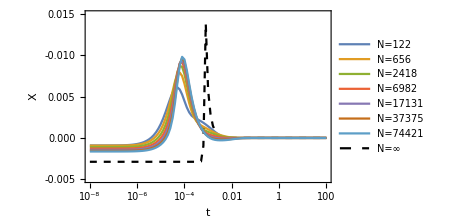

fig4a.pdf

```mathematica
filebase="data/h2o2";
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],9]];
p0=ListLogLinearPlot[Transpose[{times,concentrations[[2]]+concentrations[[3]]+concentrations[[5]]+concentrations[[7]]-(concentrations[[2,-1]]+concentrations[[3,-1]]+concentrations[[5,-1]]+concentrations[[7,-1]])}],PlotStyle->Directive[Black,Dashed],Axes->False,Frame->True,FrameLabel->{t,X},FrameTicks->{{{{-0.005,PaddedForm[-0.005,{3,3}]},{0,PaddedForm[0.,{3,3}]},{0.005,PaddedForm[0.005,{3,3}]},{0.01,PaddedForm[-0.01,{3,3}]},{0.015,PaddedForm[0.015,{3,3}]}},{{-0.005,""},{0,""},{0.005,""},{0.01,""},{0.015,""}}},{{{10^-8,HoldForm[10^("-8")]},{10^-6,HoldForm[10^("-6")]},{10^-4,HoldForm[10^("-4")]},{10^-2,HoldForm[10^("-2")]},{10^0,HoldForm[10^(0)]},{10^2,HoldForm[10^(2)]}},{{10^-8,""},{10^-6,""},{10^-4,""},{10^-2,""},{10^0,""},{10^2,""}}}},PlotRange->{{10^-8,10^2},{-0.005,0.015}},LabelStyle->Directive[Black,16],FrameStyle->Directive[AbsoluteThickness[2],Black],ImageSize->350,Joined->True,PlotRange->All];

t0=10.^-8;
t1=10^2;

rads={};
initials={};
Monitor[Do[filebase="data/dimred4/"<>ToString[i];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices)];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,dat[[2]]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
radicals=Transpose[{times,(Total/@(states.radicalnorm))-(Total/@(states.radicalnorm))[[-1]]}];AppendTo[rads,radicals];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
(*initial=Total[DeleteCases[If[#[[1]]>0, If[#[[1]]==1,DisplayForm[RowBox[{#[[2]]}]], DisplayForm[RowBox[{#[[1]],#[[2]]}]]]]&/@Transpose[{dat[[2]],spforms}],Null]];*)
initial="N="<>ToString[dim];
AppendTo[initials,initial];p=Show[p0,ListLogLinearPlot[rads,Axes->False,Frame->True,FrameLabel->{t,"Radicals"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True,PlotRange->All]];,{i,3,15,2}],{filebase,p}]
p1=Legended[p,Placed[LineLegend[Join[ColorData[97,"ColorList"][[1;;Length[initials]]],{Directive[Black,Dashed]}],Join[initials,{DisplayForm[RowBox[{"N=",∞}]]}]],Right]]
Export["fig4a.pdf",p1]
```

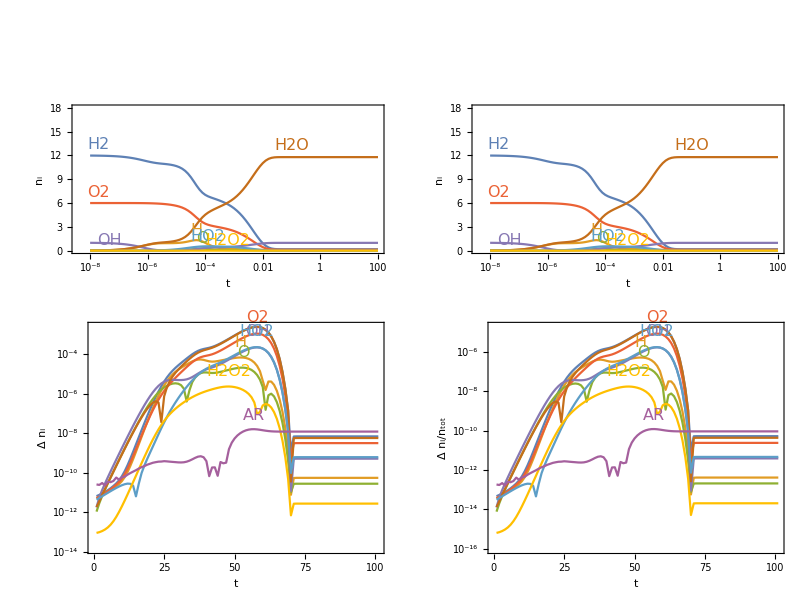

errors.pdf

```mathematica
num=6;
filebase="data/dimred4/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,dat[[2]]];
states1=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
concentrations1=Table[Transpose[{times,(Total/@(states1.concentrationnorms[[i]]))}],{i,1,ns}];
filebase="data/nodimred/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,dat[[2]]];
states2=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
concentrations2=Table[Transpose[{times,(Total/@(states2.concentrationnorms[[i]]))}],{i,1,ns}];
p=Grid[{{ListLogLinearPlot[concentrations1,PlotRange->{0,3*num},ImageSize->350,ImagePadding->{{75,15},{75,75}},Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],Axes->False,Frame->True,FrameLabel->{{Subscript[n,i],None},{t,"Full state space"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]],ListLogLinearPlot[concentrations2,PlotRange->{0,3*num},ImageSize->350,ImagePadding->{{75,15},{75,75}},Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],Axes->False,Frame->True,FrameLabel->{{Subscript[n,i],None},{t,"Dimension reduced"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]},{ListLogPlot[Abs[(concentrations1[[All,All,2]]-concentrations2[[All,All,2]])],PlotRange->All,Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],ImageSize->350,ImagePadding->{{75,15},{75,15}},Axes->False,Frame->True,FrameLabel->{{Δ * Subscript[n,i],None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]],
ListLogPlot[Transpose[Transpose[Abs[(concentrations1[[All,All,2]]-concentrations2[[All,All,2]])]]/(Total[concentrations1[[All,All,2]]])],PlotRange->All,Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],ImageSize->350,ImagePadding->{{75,15},{75,15}},Axes->False,Frame->True,FrameLabel->{{DisplayForm[RowBox[{Δ * Subscript[n,i],"/",Subscript[n,"tot"]}]],None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]}}]
Export["errors.pdf",p]
```

### fig8

```mathematica
num=4;
filebase="data/randomic/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=2*10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
AbsoluteTiming[g=Graph[#[[1]]->#[[2]]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[components=ConnectedComponents[g];]
```

{1042,9,5.9438}

{0.023652,Null}

{0.000823,Null}

```mathematica
rads={};
index=First@ToExpression[StringTrim[StringSplit[FileNames[filebase<>"states_*.npy"],"_"][[All,2]],".npy"]];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times_"<>ToString[index]<>".npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
states=Partition[Import[filebase<>"states_"<>ToString[index]<>".npy","Real64"][[17;;-1]],dim];
concentrations=Table[Transpose[{times,(Total/@(states.concentrationnorms[[i]]))}],{i,1,ns}];
temps=Transpose[{times,(Total/@(states.temperaturenorm))}];p=Grid[{{ListLogLinearPlot[concentrations,PlotRange->{-num,3*num},Joined->True,ImagePadding->{{75,75},{75,5}},ImageSize->500,PlotLabels->Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Axes->False,Frame->True,FrameLabel->{{Subscript[n,i],None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]],ListLogLinearPlot[temps,PlotRange->{0,3000},Joined->True,ImagePadding->{{75,75},{75,5}},ImageSize->500,Axes->False,Frame->True,FrameLabel->{{T,None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]}}]
Export["concentrations_temperatures.pdf",p]
```

-Graphics-

concentrations_temperatures.pdf

```mathematica
indices=ToExpression[StringTrim[StringSplit[FileNames[filebase<>"states_*.npy"],"_"][[All,2]],".npy"]]
index=indices[[5]]
states=Partition[Import[filebase<>"states_"<>ToString[index]<>".npy","Real64"][[17;;-1]],dim];Nt=Length[states];
AbsoluteTiming[componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];]
maxes=Max/@
Transpose[componentprob];
snodes=Flatten[Position[maxes,u_/;Abs[u]>10^-4]];
ptimes=(First/@Position[componentprob,#]&/@maxes[[snodes]])[[All,1]];
ptimes[[1]]=Nt;
scolors=cf/@ptimes;
edges=#[[1]]->#[[2]]&/@Import[filebase<>"edges.csv"][[2;;-1]];
AbsoluteTiming[edges=DeleteDuplicates[First@FirstPosition[components,#[[1]]]->First@FirstPosition[components,#[[2]]]&/@A2["NonzeroPositions"]];]
edges=DeleteCases[edges,u_/;u[[1]]==u[[2]]];
sizes=((Length/@components)/Total[Length/@components])^(1/2);
(Length/@components)[[#]]&/@snodes
Total[Length/@components]
N[Total[(Length/@components)[[#]]&/@snodes]/Total[Length/@components]]

AbsoluteTiming[p=LayeredGraphPlot[Graph[Range[Length[components]],edges],AspectRatio->1/2,ImageSize->dim^(1/2.)*20,EdgeStyle->Join[#->Directive[Opacity[1.0],RGBColor[1,(16*6+6)/255,(16*6+6)/255],Arrowheads[0.01],AbsoluteThickness[2]]&/@Cases[edges,u_/;MemberQ[snodes,u[[1]]]&&MemberQ[snodes,u[[2]]]],{Directive[Arrowheads[0.005],Opacity[0.5]]}],VertexSize->Table[i->{"Scaled",0.15*sizes[[i]]},{i,1,Length[sizes]}],VertexStyle->Join[Table[snodes[[i]]->Directive[EdgeForm[Opacity[0.5]],scolors[[i]]],{i,1,Length[snodes]}],{Directive[EdgeForm[AbsoluteThickness[0.25]],RGBColor[{215/255,215/255,215/255}]]}],GraphStyle->{}];]
Rasterize[p]
```

{174,275,338,432,451}

451

{0.066062,Null}

{0.522693,Null}

{41,82,168,164,9,4,2,4,2,5,5,3,4,4,5,6,5,5,5,4,6,4,4}

1042

0.519194

{2.395,Null}

-Graphics-

```mathematica
vcs=p[[1,1,2,3;;-1]]/.Disk[{x_,y_},r_]:>{x,y}/.Style[p_,s_]:>p/.DynamicName[u_,v_]:>u;
svs=p[[1,1,2,3;;-1]]/.Disk[{x_,y_},r_]:>r/.Style[p_,s_]:>p/.DynamicName[u_,v_]:>u;
ssv=p[[1,1,2,3;;-1]]/.Disk[{x_,y_},r_]:>If[Abs[r]>0,Directive[EdgeForm[AbsoluteThickness[0.25]],RGBColor[{215/255,215/255,215/255}]],r]/.Style[p_,s_]:>s/.DynamicName[u_,v_]:>u;
ssv[[snodes]]=Table[Directive[EdgeForm[AbsoluteThickness[0.25]],scolors[[i]]],{i,1,Length[scolors]}];
ssv[[First@FirstPosition[components,1+index]]]=Directive[EdgeForm[AbsoluteThickness[0.25]],Red];
vcs[[3,2]]=10;
vcs[[2,2]]=0;
vcs[[1,2]]=-20;
ed=p[[1,1,1]]/.DynamicName[u_]:>u/.Arrow[BezierCurve[{DynamicLocation[s1_,Automatic,Center],l__,DynamicLocation[s2_,Automatic,Center]}]]:>Arrow[BezierCurve[Join[{vcs[[ToExpression[StringSplit[s1,"$"][[2]]]]]},{l},{vcs[[ToExpression[StringSplit[s2,"$"][[2]]]]]}]],{0,svs[[ToExpression[StringSplit[s2,"$"][[2]]]]]}]/.Arrow[{DynamicLocation[s1_,Automatic,Center],DynamicLocation[s2_,Automatic,Center]}]:>Arrow[{vcs[[ToExpression[StringSplit[s1,"$"][[2]]]]],vcs[[ToExpression[StringSplit[s2,"$"][[2]]]]]},{0,svs[[ToExpression[StringSplit[s2,"$"][[2]]]]]}]/.DynamicName[u_,v_]:>u;
vd=Join[{Directive[Hue[0.6, 0.2, 0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]],Directive[EdgeForm[],GrayLevel[0]]},Flatten[Table[{ssv[[i]],Disk[vcs[[i]],svs[[i]]]},{i,1,Length[vcs]}]]];
plot=Graphics[{ed,vd},ImageSize->dim^(1/2.)*20]
plot2=Graphics[{ed,vd},ImageSize->1000]
Export[filebase<>"_"<>ToString[index]<>"_scaledconnected.pdf",plot]
Export[filebase<>"_"<>ToString[index]<>"_connected.pdf",plot2]
```

-Graphics-

-Graphics-

data/randomic/4_451_scaledconnected.pdf

data/randomic/4_451_connected.pdf

#### large graph random initial conditions

```mathematica
num=10;
filebase="data/nodimred/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
AbsoluteTiming[g=Graph[#[[1]]->#[[2]]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[components=ConnectedComponents[g];]
```

{63835,9,0}

{1.97676,Null}

{0.092066,Null}

```mathematica
rads={};
indices=ToExpression[StringTrim[StringSplit[FileNames[filebase<>"states_*.npy"],"_"][[All,2]],".npy"]]
index=indices[[2]]
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times_"<>ToString[index]<>".npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
states=Partition[Import[filebase<>"states_"<>ToString[index]<>".npy","Real64"][[17;;-1]],dim];
concentrations=Table[Transpose[{times,(Total/@(states.concentrationnorms[[i]]))}],{i,1,ns}];
temps=Transpose[{times,(Total/@(states.temperaturenorm))}];p=Grid[{{ListLogLinearPlot[concentrations,PlotRange->{-num,3*num},Joined->True,ImagePadding->{{75,75},{75,5}},ImageSize->500,PlotLabels->Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Axes->False,Frame->True,FrameLabel->{{Subscript[n,i],None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]],ListLogLinearPlot[temps,PlotRange->{0,3000},Joined->True,ImagePadding->{{75,75},{75,5}},ImageSize->500,Axes->False,Frame->True,FrameLabel->{{T,None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]}}]
Export["concentrations_temperatures.pdf",p]
```

{19731,20463,2096,2102,21758,2583,2710,3002,33867,4714}

20463

-Graphics-

concentrations_temperatures.pdf

```mathematica
indices=ToExpression[StringTrim[StringSplit[FileNames[filebase<>"states_*.npy"],"_"][[All,2]],".npy"]]
index=indices[[2]]
states=Partition[Import[filebase<>"states_"<>ToString[index]<>".npy","Real64"][[17;;-1]],dim];Nt=Length[states];
AbsoluteTiming[componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];]
maxes=Max/@
Transpose[componentprob];
snodes=Flatten[Position[maxes,u_/;Abs[u]>10^-4]];
ptimes=(First/@Position[componentprob,#]&/@maxes[[snodes]])[[All,1]];
ptimes[[1]]=Nt;
scolors=cf/@ptimes;
edges=#[[1]]->#[[2]]&/@Import[filebase<>"edges.csv"][[2;;-1]];
sizes=((Length/@components)/Total[Length/@components])^(1/2);
vcs=#[[1]]->{3/4*#[[3]],#[[4]]}&/@Import[filebase<>"nodes.csv"][[2;;-1]];

layers=Sort[DeleteDuplicates[vcs[[All,2,2]]]];
edgecoordinates[e_]:=Module[{start,end},{start,end}={#[[1]]/.vcs,#[[2]]/.vcs}&@e;
{start,{start[[1]],end[[2]]},end}]
edgecoordinates[e_]:=Module[{start,end},{start,end}={#[[1]]/.vcs,#[[2]]/.vcs}&@e;
{start,{start[[1]],start[[2]]+(end[[2]]-start[[2]])*0.5},end}]
ecs=edgecoordinates/@Complement[edges,Cases[edges,u_/;MemberQ[snodes,u[[1]]]&&MemberQ[snodes,u[[2]]]]];
ecs2={#[[1]]/.vcs,#[[2]]/.vcs}&/@Cases[edges,u_/;MemberQ[snodes,u[[1]]]&&MemberQ[snodes,u[[2]]]];
offsets=sizes[[#[[2]]]]&/@Cases[edges,u_/;MemberQ[snodes,u[[1]]]&&MemberQ[snodes,u[[2]]]];
p=Graphics[{Directive[Opacity[0.7],Hue[0.6, 0.7, 0.5]],Arrowheads[0],Directive[Arrowheads[0],AbsoluteThickness[0.5],Opacity[0.1]],Arrow[BSplineCurve[#]]&/@ecs,Directive[ColorData[97,"ColorList"][[4]],Arrowheads[0.01],AbsoluteThickness[1],Opacity[0.5]],Arrow[BSplineCurve[#[[1]]],{0,0.4*#[[2]]}]&/@Transpose[{ecs2,offsets}],Opacity[1],EdgeForm[],Table[{Directive[EdgeForm[Directive[Opacity[0.5],AbsoluteThickness[0.3]]],RGBColor[215/255,215/255,215/255]],Disk[vcs[[i,2]],0.4*sizes[[i]]]},{i,Complement[Range[Length[vcs]],snodes]}],Table[{EdgeForm[Directive[Black,Opacity[0.5],AbsoluteThickness[0.3]]],scolors[[First@FirstPosition[snodes,i]]],Disk[vcs[[i,2]],0.4*sizes[[i]]]},{i,snodes}]},ImageSize->1000];
Rasterize[p]
```

{19731,20463,2096,2102,21758,2583,2710,3002,33867,4714}

20463

{2.59962,Null}

-Graphics-

#### Create csv of graphviz output

```mathematica
AbsoluteTiming[lines=StringSplit[ReadList[ToString[num]<>"_layered.gr","String"][[5;;-2]]];];
AbsoluteTiming[edgelines=Cases[lines,u_/;Head[ToExpression[u[[1]]]]==Rule];];
AbsoluteTiming[nodelines=Cases[lines,u_/;Head[ToExpression[u[[1]]]]==Integer];];
AbsoluteTiming[ecs=Partition[Internal`StringToDouble/@StringTrim[Flatten[StringSplit[#[[2;;-1]],","]],("[pos=\""|"\"];")],2]&/@edgelines;]
AbsoluteTiming[vcs=Partition[Internal`StringToDouble[#]&/@Flatten[StringSplit[StringTrim[#,("pos=\""|"\",")]&/@nodelines[[All,3]],","]],2];]
{xmin,xmax}={Min[vcs[[All,1]]],Max[vcs[[All,1]]]};
{ymin,ymax}={Min[vcs[[All,2]]],Max[vcs[[All,2]]]};
r=1;
ecs={r*(#[[1]]-xmin)/(xmax-xmin),(#[[2]]-ymin)/(ymax-ymin)}&/@#&/@ecs;
vcs={r*(#[[1]]-xmin)/(xmax-xmin),(#[[2]]-ymin)/(ymax-ymin)}&/@vcs;

y1=0.3;
transform[{x_,y_}]:={x+Sign[vcs[[1,1]]-0.5]*(y-1)*0.75,Tanh[0.1+y/y1]};
transform[{x_,y_}]:={2*x,y};
sedges=Flatten[Position[ToExpression[edgelines[[All,1]]],u_/;Length[u]>0&&MemberQ[snodes,u[[1]]]&&MemberQ[snodes,u[[2]]]]];
AbsoluteTiming[ecs2=transform/@#&/@ecs;]
AbsoluteTiming[vcs2=transform/@vcs;]
nodeids=ToExpression[nodelines[[All,1]]];
sourceids=ToExpression[edgelines[[All,1]]][[All,1]];
sinkids=ToExpression[edgelines[[All,1]]][[All,2]];
sizes=Length/@components;
Export[ToString[num]<>"_nodes.csv",Flatten/@Transpose[{nodeids,vcs2,sizes}]]
Export[ToString[num]<>"_edges.csv",Flatten/@Transpose[{sourceids,sinkids,ecs2}]]
```

{3.01083,Null}

{0.065253,Null}

{0.584627,Null}

{0.008256,Null}

10_nodes.csv

10_edges.csv

```mathematica
nodes=Import["10_nodes.csv"];
edges=Import["10_edges.csv"];

vcs=nodes[[All,{2,3}]];
AbsoluteTiming[ecs=Partition[#,2]&/@edges[[All,3;;-1]];]
sizes=0.05*(nodes[[All,4]]/Total[nodes[[All,4]]])^(1/2);
p=Graphics[{Arrowheads[0],Directive[Opacity[0.7],Hue[0.6, 0.7, 0.5]],Opacity[0.1],Arrow[BezierCurve[#]]&/@ecs,Opacity[1],Black,Table[{If[MemberQ[snodes,i],scolors[[First@FirstPosition[snodes,i]]],Black],Disk[vcs[[i]],sizes[[i]]]},{i,1,Length[vcs]}]},ImageSize->1000,PlotRange->All];
Rasterize[p]
```

{0.210733,Null}

#### Plots for each case

```mathematica
Monitor[Do[
filebase="data/nodimred/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
AbsoluteTiming[g=Graph[#[[1]]->#[[2]]&/@A2["NonzeroPositions"]];];
AbsoluteTiming[components=ConnectedComponents[g];];

states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];Nt=Length[states];
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
ptimes=(First/@Position[componentprob,#]&/@maxes)[[All,1]];
ptimes[[1]]=Nt;
snodes=Flatten[Position[maxes,u_/;Abs[u]>10^-4]];
scolors=cf/@ptimes[[snodes]];

AbsoluteTiming[lines=StringSplit[ReadList[ToString[num]<>"_layered.gr","String"][[5;;-2]]];];
AbsoluteTiming[edgelines=Cases[lines,u_/;Head[ToExpression[u[[1]]]]==Rule];];
AbsoluteTiming[nodelines=Cases[lines,u_/;Head[ToExpression[u[[1]]]]==Integer];];
AbsoluteTiming[ecs=Partition[Internal`StringToDouble/@StringTrim[Flatten[StringSplit[#[[2;;-1]],","]],("[pos=\""|"\"];")],2]&/@edgelines;];
AbsoluteTiming[vcs=Partition[Internal`StringToDouble[#]&/@Flatten[StringSplit[StringTrim[#,("pos=\""|"\",")]&/@nodelines[[All,3]],","]],2];];
{xmin,xmax}={Min[vcs[[All,1]]],Max[vcs[[All,1]]]};
{ymin,ymax}={Min[vcs[[All,2]]],Max[vcs[[All,2]]]};
r=1;
ecs={r*(#[[1]]-xmin)/(xmax-xmin),(#[[2]]-ymin)/(ymax-ymin)}&/@#&/@ecs;
vcs={r*(#[[1]]-xmin)/(xmax-xmin),(#[[2]]-ymin)/(ymax-ymin)}&/@vcs;

sizes=Table[(10^-6+0.1*N[Length[components[[i]]]/dim]^(1/2)),{i,1,Length[components]}];
y1=0.3;
transform[{x_,y_}]:={x+Sign[vcs[[1,1]]-0.5]*(y-1)*0.75,Tanh[0.1+y/y1]};
sedges=Flatten[Position[ToExpression[edgelines[[All,1]]],u_/;Length[u]>0&&MemberQ[snodes,u[[1]]]&&MemberQ[snodes,u[[2]]]]];
ecs2=transform/@#&/@ecs;
vcs2=transform/@vcs;
sizes=Table[(10^-8+0.05*N[Length[components[[i]]]/dim]^(1/2)),{i,1,Length[components]}];
p=Graphics[{Arrowheads[0],Directive[AbsoluteThickness[0.1],Opacity[0.7],LightGray],Arrow[BezierCurve[#]]&/@ecs2,Directive[AbsoluteThickness[1],Opacity[0.7],Hue[0.6, 0.7, 0.5]],Arrowheads[0.02],Opacity[1],Arrow[BezierCurve[#],{0,0.015}]&/@ecs2[[sedges]],Opacity[1],Black,Table[Disk[vcs2[[i]],sizes[[i]]],{i,1,Length[vcs]}],Table[{scolors[[First@FirstPosition[snodes,i]]],Disk[vcs2[[i]],sizes[[i]]]},{i,snodes}]},ImageSize->500,PlotRange->{Automatic,{-0,1.1}}];
Export[ToString[num]<>"components.pdf",p];,{num,4,10}],num]
```

```mathematica
AbsoluteTiming[lines=StringSplit[ReadList["4_layered.gr","String"][[5;;-2]]];];
AbsoluteTiming[edgelines=Cases[lines,u_/;Head[ToExpression[u[[1]]]]==Rule];];
AbsoluteTiming[nodelines=Cases[lines,u_/;Head[ToExpression[u[[1]]]]==Integer];];
AbsoluteTiming[ecs=Partition[Internal`StringToDouble/@StringTrim[Flatten[StringSplit[#[[2;;-1]],","]],("[pos=\""|"\"];")],2]&/@edgelines;]
AbsoluteTiming[vcs=Partition[Internal`StringToDouble[#]&/@Flatten[StringSplit[StringTrim[#,("pos=\""|"\",")]&/@nodelines[[All,3]],","]],2];]
{xmin,xmax}={Min[ecs[[All,All,1]]],Max[ecs[[All,All,1]]]};
{ymin,ymax}={Min[ecs[[All,All,2]]],Max[ecs[[All,All,2]]]};
ecs={2*(#[[1]]-xmin)/(xmax-xmin),(#[[2]]-ymin)/(ymax-ymin)}&/@#&/@ecs;
vcs={2*(#[[1]]-xmin)/(xmax-xmin),(#[[2]]-ymin)/(ymax-ymin)}&/@vcs;

AbsoluteTiming[Monitor[Do[
sizes=ConstantArray[0.002,Length[components]];
positions=First/@Position[Abs[Total[states[[tind,#]]]]&/@components,u_/;Abs[u]>10^-4];
sizes[[positions]]=0.002+0.005*Log[(Abs[Total[states[[tind,#]]]]&/@components)[[positions]]/10^-4]/4;
p=Graphics[{Arrowheads[0],Directive[Opacity[0.7],Hue[0.6, 0.7, 0.5]],Opacity[0.1],Arrow[BezierCurve[#]]&/@ecs,Opacity[1],Black,Table[Disk[vcs[[i]],sizes[[i]]],{i,1,Length[vcs]}]},ImageSize->1000,PlotRange->{{-0.5,2.5},{-0.25,1.25}}];
Export["animation2/"<>IntegerString[tind,10,4]<>".png",p];,{tind,1,100}],{tind}]]
```

{2.84856,Null}

{0.067717,Null}

#### Create graphviz input files

data/nodimred/10

{63835,9,0}

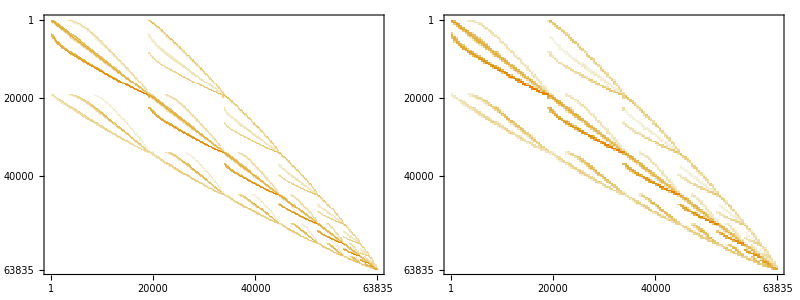

{2.2716,Null}

{0.06859,Null}

6960

{822.278,Null}

data/nodimred/10edges.csv

{0.216219,Null}

```mathematica
filebase="data/nodimred/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
Grid[{{MatrixPlot[A],MatrixPlot[A2]}}]

AbsoluteTiming[g=Graph[#[[1]]->#[[2]]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[components=ConnectedComponents[g];]

Length[ConnectedComponents[g]]
Monitor[AbsoluteTiming[edges=Flatten[Table[Table[If[Max[Abs[A2[[components[[i]],components[[j]]]]]]>0&&i!=j,i->j,{}],{j,1,i}],{i,1,Length[components]}]];],{i}]
Export[filebase<>"edges.csv",Join[{{"Source","Target"}},{#[[1]],#[[2]]}&/@edges]]
AbsoluteTiming[g=Graph[Range[Length[components]],edges,GraphLayout->{"VertexLayout"->"LayeredDigraphEmbedding"},ImageSize->{Automatic,500},AspectRatio->1/2,VertexSize->0.002*Length[components],PerformanceGoal->"Quality",VertexStyle->{Directive[Black]},EdgeStyle->Directive[Opacity[0.1],Arrowheads[0]]];]
```

```mathematica
filebases=Table["data/nodimred/"<>ToString[i],{i,3,10}]
Do[
AbsoluteTiming[edges=#[[1]]->#[[2]]&/@Import[filebase<>"edges.csv"][[2;;-1]];];
file=OpenWrite[filebase<>".gr"];
WriteLine[file,"digraph{"];
WriteLine[file,"ratio=0.5"];
WriteLine[file,"size=8.5"];
WriteLine[file,"edge[arrowhead=\"none\"]"];
WriteLine[file,"node[shape=circle label=\"\" style=filled fillcolor=black]"];
AbsoluteTiming[WriteLine[file,#]&/@Range[Max[edges[[All,1]]]];];
AbsoluteTiming[WriteLine[file,#[[1]]->#[[2]]]&/@edges;];
WriteLine[file,"}"];
Close[file];,{filebase,filebases}]
```

{data/nodimred/3,data/nodimred/4,data/nodimred/5,data/nodimred/6,data/nodimred/7,data/nodimred/8,data/nodimred/9,data/nodimred/10}

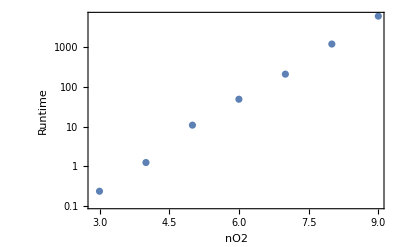

layeredruntimes.pdf

{0.000399394,0.00216294,0.0117136,0.0634356,0.34354,1.86046,10.0755}

```mathematica
rtimes={{3,0.232},{4,1.232},{5,10.838},{6,48.907},{7,3*60+30.229},{8,20*60+12.052},{9,102*60+21.989}};
p=ListLogPlot[rtimes,Axes->False,Frame->True,FrameLabel->{"nO2","Runtime"},LabelStyle->Directive[16,Black]]
Export["layeredruntimes.pdf",p]
Table[1/3600.*10^Fit[{#[[1]],Log[#[[2]]]/Log[10]}&/@rtimes,{1,x},x]/.x->X,{X,4,10}]
```

### fig 9

data/dimred4/10

{11129,9,124.557}

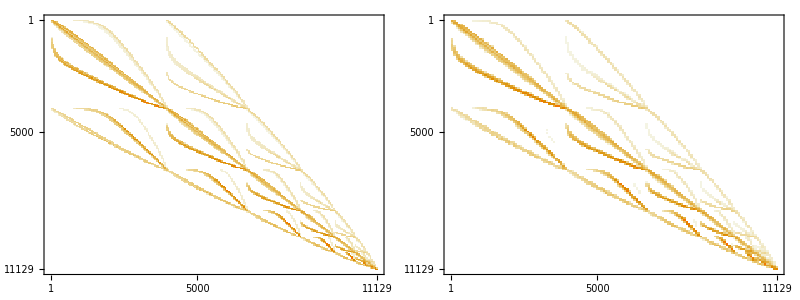

{0.434501,Null}

{0.01076,Null}

6

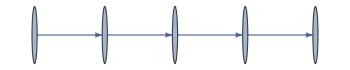

```mathematica
filebase="data/dimred4/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=1*10^-3;
thrs=1*10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
Grid[{{MatrixPlot[A],MatrixPlot[A2]}}]

AbsoluteTiming[g=Graph[#[[1]]->#[[2]]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[components=ConnectedComponents[g];]

Length[ConnectedComponents[g]]
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
components=Extract[components,Position[maxes,u_/;Abs[u]>10^-3]];
vsizes=Table[i->2*Length[components]*(0.01+0.05*N[Length[components[[i]]]/dim]^(1/2)),{i,1,Length[components]}];
vstyles=Table[i->If[MemberQ[components[[i]],First@FirstPosition[multiindices,dat[[2]]]],Black,White],{i,1,Length[components]}];

g=Graph[Range[Length[components]],Flatten[Table[If[Max[Abs[A2[[components[[i]],components[[j]]]]]]>0&&i!=j,i->j,{}],{i,1,Length[components]},{j,1,Length[components]}]]];
p=GraphPlot[g,ImageSize->350]
```

```mathematica
Nt=Length[states];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
ptimes=(First/@Position[componentprob,#]&/@maxes)[[All,1]];
complayers=Round[LayeredGraphPlot[g,Left,VertexSize->vsizes,VertexStyle->Table[i->cf[ptimes[[i]]],{i,1,Length[components]}],ImageSize->400,ImagePadding->{{75,15},{75,15}}][[1,1,1;;Length[components],1]]];
layers=Sort[DeleteDuplicates[complayers]];
ptimes[[First@FirstPosition[complayers,0]]]=Nt;
compconcentrations=Transpose[Table[Mean[N[#[[i]]]&/@multiindices[[Flatten[Extract[components,Position[complayers,lay]]]]]],{lay,layers},{i,1,ns}]];
compconcentrations=Transpose[Table[maxes=Max/@Transpose[states[[All,Flatten[Extract[components,Position[complayers,lay]]]]]];
comp=N[#[[i]]]&/@multiindices[[Flatten[Extract[components,Position[complayers,lay]]]]];
Total[maxes/Total[maxes]*comp],{lay,Sort[layers]},{i,1,ns}]];
First@FirstPosition[complayers,1-Length[layers]]
First@FirstPosition[complayers,2-Length[layers]]
First@FirstPosition[complayers,4-Length[layers]]
First@FirstPosition[complayers,0]
```

5

4

2

1

```mathematica
Length[components]
Length/@components
multiindices[[components[[All,1]]]]
VertexStyle->Table[i->cf[ptimes[[i]]],{i,1,Length[components]}]
VertexSize->vsizes
```

5

{2451,1813,2797,4066,1}

{{14,0,0,7,1,6,0,0,200},{16,0,0,8,1,4,0,0,200},{18,0,0,9,1,2,0,0,200},{19,1,0,10,0,1,0,0,200},{20,0,0,10,1,0,0,0,200}}

VertexStyle→{1→RGBColor[0., 0.6666666666666666, 0.],2→RGBColor[0.4983498349834983, 0.4158415841584158, 0.834983498349835],3→RGBColor[0.5115511551155115, 0.42244224422442245, 0.8217821782178218],4→RGBColor[0.6303630363036303, 0.4818481848184818, 0.702970297029703],5→RGBColor[0.9867986798679867, 0.6600660066006601, 0.3465346534653465]}

VertexSize→{1→0.334646,2→0.301809,3→0.350662,4→0.402222,5→0.10474}

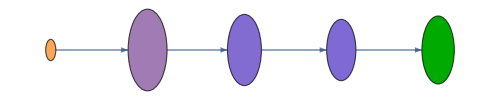

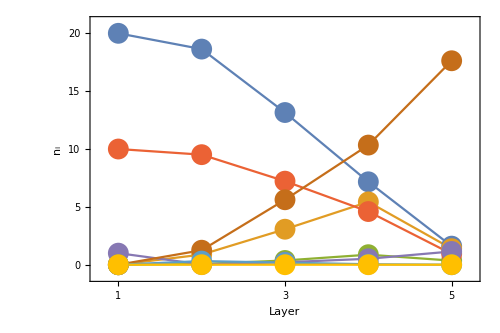

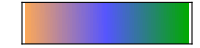

plots/smalldag.pdf

plots/cb1.pdf

plots/concentrations.pdf

```mathematica
p1=LayeredGraphPlot[g,Left,VertexSize->vsizes,VertexStyle->Table[i->cf[ptimes[[i]]],{i,1,Length[components]}],ImageSize->500,ImagePadding->{{75,75},{5,5}}]/.Arrow[{i_,j_},u_]:>Arrow[{i,j},0.5*{i/.vsizes,j/.vsizes}]/.Arrow[BezierCurve[l_],u_]:>Arrow[BezierCurve[l],0.5*{l[[1]]/.vsizes,l[[-1]]/.vsizes}]

p=Show[ListPlot[compconcentrations,Joined->True,Axes->False,Frame->True,FrameLabel->{"Layer",Subscript[n,i]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{0.75,Length[layers]+0.25},{-1,21}},FrameTicks->{{Table[i,{i,0,20,5}],Table[{i,""},{i,0,20,5}]},{Table[i,{i,1,Length[layers],2}],Table[{i,""},{i,1,Length[layers],2}]}},ImageSize->500,ImagePadding->{{75,75},{75,15}},AspectRatio->2/3],ListPlot[compconcentrations,Joined->False,PlotStyle->Directive[PointSize[0.03]]]]
cb1
Export["plots/smalldag.pdf",p1]
Export["plots/cb1.pdf",cb1]
Export["plots/concentrations.pdf",p]
```

```mathematica
p1=LayeredGraphPlot[g,Left,VertexSize->vsizes,VertexStyle->Table[i->cf[ptimes[[i]]],{i,1,Length[components]}],ImageSize->500,ImagePadding->{{75,75},{5,5}}]/.Arrow[{i_,j_},u_]:>Arrow[{i,j},0.5*{i/.vsizes,j/.vsizes}]/.Arrow[BezierCurve[l_],u_]:>Arrow[BezierCurve[l],0.5*{l[[1]]/.vsizes,l[[-1]]/.vsizes}];
p2=Show[ListPlot[compconcentrations,Joined->True,Axes->False,Frame->True,FrameLabel->{"Layer",Subscript[n,i]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{0.75,Length[layers]+0.25},{-1,21}},FrameTicks->{{Table[i,{i,0,20,5}],Table[{i,""},{i,0,20,5}]},{Table[i,{i,1,Length[layers],2}],Table[{i,""},{i,1,Length[layers],2}]}},PlotLabels->Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,Length[species]}],ImageSize->500,ImagePadding->{{75,75},{75,15}},AspectRatio->2/3],ListPlot[compconcentrations,Joined->False,PlotStyle->Directive[PointSize[0.03]]]];
p=Grid[{{cb1},{p1},{p2}}]
Export["fig5.pdf",p]
```

-Graphics-

fig5.pdf

### fig10

```mathematica
filebase="data/dimred4/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=1*10^-3;
thrs=2*10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
AbsoluteTiming[edges2=#[[1]]->#[[2]]&/@A2["NonzeroPositions"];]
AbsoluteTiming[g=Graph[Range[dim],edges2];]
components=ConnectedComponents[g];
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
components=Intersection[show,#]&/@Reverse[Extract[components,Position[maxes,u_/;Abs[u]>10^-3]]];
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
show=Flatten[components];

AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"SpringElectricalEmbedding","EdgeLayout"->"StraightLine"}];]
AbsoluteTiming[vsizes=Table[0.02+0.5*states[[-1,i]],{i,1,dim}];]

Length[show]
AbsoluteTiming[edges3=Flatten[If[MemberQ[show,#[[1]]]&&MemberQ[show,#[[2]]],#[[1]]->#[[2]],{}]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[g=Graph[show,edges3];]
AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"SpringElectricalEmbedding","EdgeLayout"->"StraightLine"}];]
{xmax,xmin}={Max[vcs[[All,1]]],Min[vcs[[All,1]]]};
{ymax,ymin}={Max[vcs[[All,2]]],Min[vcs[[All,2]]]};
vcs=10*{2*#[[1]]/(xmax-xmin),#[[2]]/(ymax-ymin)}&/@vcs;
vsizes=Table[0.02+0.5*states[[-1,i]],{i,show}];
```

data/dimred4/10

{11129,9,124.557}

{0.338641,Null}

{0.13363,Null}

{4.93637,Null}

{0.132482,Null}

1815

{9.77162,Null}

{0.043844,Null}

{0.717361,Null}

```mathematica
vcs2={};
x0=0;
dx=1.5;
dy=3;
orientations=ConstantArray[1,Length[components]];
(*orientations[[2]]=orientations[[3]]=orientations[[5]]=-1;*)
orientations[[1]]=orientations[[3]]=orientations[[4]]=orientations[[5]]=-1;
Do[
emb=Reverse/@GraphEmbedding[Graph[components[[cid]],Cases[edges3,u_/;MemberQ[components[[cid]],u[[1]]]&&MemberQ[components[[cid]],u[[2]]]]]];
If[orientations[[cid]]==-1,emb={-#[[1]],-#[[2]]}&/@emb,emb={-#[[1]],#[[2]]}&/@emb];
{xmax,xmin}={Max[emb[[All,1]]],Min[emb[[All,1]]]};
{ymax,ymin}={Max[emb[[All,2]]],Min[emb[[All,2]]]};
If[xmax>xmin&&ymax>ymin,emb={dx*cid+(#[[1]]-xmin)/(xmax-xmin),dy*(#[[2]]-ymin)/(ymax-ymin)}&/@emb;,emb={dx*cid+dx/2,dy/2}&/@emb;];
vcs2=Join[vcs2,Table[components[[cid,i]]->emb[[i]],{i,1,Length[emb]}]];,{cid,1,Length[components]}]
vcs3=show/.vcs2;
maxes2=Max[states[[All,#]]]&/@show;
ptimes2=Last@FirstPosition[states[[All,#]],maxes2[[First@FirstPosition[show,#]]]]&/@show;
(*ptimes2=ptimes2/.u_/;u>70:>Nt;*)
vstyles=Table[cf[ptimes2[[i]]],{i,1,Length[show]}];
AbsoluteTiming[Monitor[fluxes=Table[Abs[A2[[#[[1]],#[[2]]]]*states[[nt,#[[1]]]]-A2[[#[[2]],#[[1]]]]*states[[nt,#[[2]]]]]/10^1&/@edges2,{nt,1,100}];,nt]]
maxfluxes=Max/@Transpose[fluxes];
AbsoluteTiming[Monitor[fluxtimes=Table[First@FirstPosition[fluxes[[All,i]],maxfluxes[[i]]],{i,1,Length[maxfluxes]}];,i]]
vsizes2=Table[0.02+0.1*Log[Max[maxes2[[i]],10^-4]/10^-4]/4,{i,1,Length[show]}];
```

{111.113,Null}

{2.70396,Null}

{8.36315,Null}

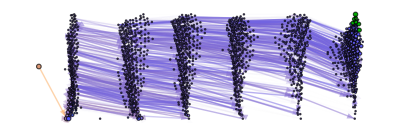

fig6.pdf

```mathematica
AbsoluteTiming[ptimes2=First@Position[states[[All,#]],u_/;u>0.9*maxes2[[First@FirstPosition[show,#]]]][[-1]]&/@show;]
vstyles=Table[cf[ptimes2[[i]]],{i,1,Length[show]}];
vsizes2=Table[0.02+0.02*Log[Max[maxes2[[i]],10^-4]/10^-4]/4,{i,1,Length[show]}];
p=Graphics[Join[{Arrowheads[0.007],Directive[Opacity[0.7],Hue[0.6,0.7,0.5]],Opacity[0.1]},{Opacity[Min[0.5,maxfluxes[[#]]/10^1]],cf[fluxtimes[[#]]],Arrow[{vcs3[[First@FirstPosition[show,edges3[[#,1]]]]],vcs3[[First@FirstPosition[show,edges3[[#,2]]]]]},Max[0,vsizes2[[First@FirstPosition[show,edges3[[#,2]]]]]]]}&/@Range[Length[edges3]],{Opacity[1],Directive[Hue[0.6,0.2,0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]]},{vstyles[[#]],Disk[vcs3[[#]],vsizes2[[#]]]}&/@SortBy[Range[Length[show]],ptimes2[[#]]&]],ImageSize->{Automatic,500},ImagePadding->{{ImageScaled[0.05],ImageScaled[0.05]},{ImageScaled[0.05],ImageScaled[0.05]}}]
Export["fig6.pdf",p]
```

#### Create CSVs

```mathematica
filebase="data/nodimred/10";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
Export[filebase<>"rows.csv",Transpose[{rows}]]
Export[filebase<>"columns.csv",Transpose[{columns}]]
Export[filebase<>"data.csv",Transpose[{data}]]
Export[filebase<>"w_sparse.csv",Transpose[{rows,columns,data}]]
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
Export[filebase<>"states.csv",states]
```

{63835,9,0}

data/nodimred/10rows.csv

data/nodimred/10columns.csv

data/nodimred/10data.csv

data/nodimred/10w_sparse.csv

### animation

```mathematica
filebase="data/dimred3/10"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];
AbsoluteTiming[edges2=#[[1]]->#[[2]]&/@A2["NonzeroPositions"];]
AbsoluteTiming[g=Graph[Range[dim],edges2];]
AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"SpringElectricalEmbedding","EdgeLayout"->"StraightLine"}];]
AbsoluteTiming[vsizes=Table[0.02+0.5*states[[-1,i]],{i,1,dim}];]
```

data/dimred3/10

{11106,9,0}

{0.210168,Null}

{0.068284,Null}

{3.07406,Null}

{0.093653,Null}

```mathematica
Dimensions[Max/@Transpose[states]]
show=First/@Position[Max/@Transpose[states],u_/;Abs[u]>10^-8];
Length[show]
AbsoluteTiming[edges3=Flatten[If[MemberQ[show,#[[1]]]&&MemberQ[show,#[[2]]],#[[1]]->#[[2]],{}]&/@A2["NonzeroPositions"]];]
AbsoluteTiming[g=Graph[show,edges3];]
AbsoluteTiming[vcs=GraphEmbedding[g,{"VertexLayout"->"SpringElectricalEmbedding","EdgeLayout"->"StraightLine"}];]
{xmax,xmin}={Max[vcs[[All,1]]],Min[vcs[[All,1]]]};
{ymax,ymin}={Max[vcs[[All,2]]],Min[vcs[[All,2]]]};
vcs=10*{2*#[[1]]/(xmax-xmin),#[[2]]/(ymax-ymin)}&/@vcs;
vsizes=Table[0.02+0.5*states[[-1,i]],{i,show}];
```

{11106}

1819

{15.0901,Null}

{0.031323,Null}

{0.372186,Null}

```mathematica
AbsoluteTiming[g=Graph[Range[dim],edges2];]
components=ConnectedComponents[g];
componentprob=Table[Total[states[[i,components[[j]]]]],{i,1,Length[states]},{j,1,Length[components]}];
maxes=Max/@
Transpose[componentprob];
components=Intersection[show,#]&/@Reverse[Extract[components,Position[maxes,u_/;Abs[u]>10^-8]]];

vcs2={};
x0=0;
dx=1.5;
dy=4;
orientations=ConstantArray[1,Length[components]];
orientations[[2]]=-1;
orientations[[3]]=-1;
Do[
emb=Reverse/@GraphEmbedding[Graph[components[[cid]],Cases[edges3,u_/;MemberQ[components[[cid]],u[[1]]]&&MemberQ[components[[cid]],u[[2]]]]]];
If[orientations[[cid]]==-1,emb={-#[[1]],-#[[2]]}&/@emb,emb={-#[[1]],#[[2]]}&/@emb];
{xmax,xmin}={Max[emb[[All,1]]],Min[emb[[All,1]]]};
{ymax,ymin}={Max[emb[[All,2]]],Min[emb[[All,2]]]};
If[xmax>xmin&&ymax>ymin,emb={dx*cid+(#[[1]]-xmin)/(xmax-xmin),dy*(#[[2]]-ymin)/(ymax-ymin)}&/@emb;,emb={dx*cid+dx/2,dy/2}&/@emb;];
vcs2=Join[vcs2,Table[components[[cid,i]]->emb[[i]],{i,1,Length[emb]}]];,{cid,1,Length[components]}]
vcs3=show/.vcs2;
Rasterize[Graphics[Join[{Arrowheads[0.007],Directive[Opacity[0.7],Hue[0.6,0.7,0.5]],Opacity[0.1]},Arrow[{vcs3[[First@FirstPosition[show,#[[1]]]]],vcs3[[First@FirstPosition[show,#[[2]]]]]},Max[0,vsizes[[First@FirstPosition[show,#[[2]]]]]]]&/@edges3,{Opacity[1],Directive[Hue[0.6,0.2,0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]]},Disk[vcs3[[First@FirstPosition[show,#]]],vsizes[[First@FirstPosition[show,#]]]]&/@show],ImageSize->{Automatic,500},ImagePadding->{{ImageScaled[0.05],ImageScaled[0.05]},{ImageScaled[0.05],ImageScaled[0.05]}}]]
```

{0.069757,Null}

-Graphics-

```mathematica
{xmax,xmin}={Max[vcs3[[All,1]]],Min[vcs3[[All,1]]]};
{ymax,ymin}={Max[vcs3[[All,2]]],Min[vcs3[[All,2]]]};
AbsoluteTiming[ParallelDo[vsizes=Table[0.02+0.1*Log[Max[states[[nt,i]],10^-4]/10^-4]/4,{i,show}];
plot=Graphics[Join[{Arrowheads[0.007],Directive[Opacity[0.7],Hue[0.6,0.7,0.5]],Opacity[0.5]},{Opacity[Min[0.5,Abs[A2[[#[[1]],#[[2]]]]*states[[nt,#[[1]]]]-A2[[#[[2]],#[[1]]]]*states[[nt,#[[2]]]]]/10^1]],Arrow[{vcs3[[First@FirstPosition[show,#[[1]]]]],vcs3[[First@FirstPosition[show,#[[2]]]]]},{0,Max[0,vsizes[[First@FirstPosition[show,#[[2]]]]]]}]}&/@edges3,{Opacity[1],Directive[Hue[0.6,0.2,0.8],EdgeForm[Directive[GrayLevel[0],Opacity[0.7]]]]},Disk[vcs3[[First@FirstPosition[show,#]]],vsizes[[First@FirstPosition[show,#]]]]&/@show],ImageSize->{Automatic,500},ImagePadding->{{ImageScaled[0.05],ImageScaled[0.05]},{ImageScaled[0.05],ImageScaled[0.05]}},PlotRange->{{xmin-1/2,xmax+1/2},{ymin-1/2,ymax+1/2}}];
Export["animation/"<>IntegerString[nt,10,4]<>".png",plot,ImageSize->1000];,{nt,1,100}]]
```

### errors

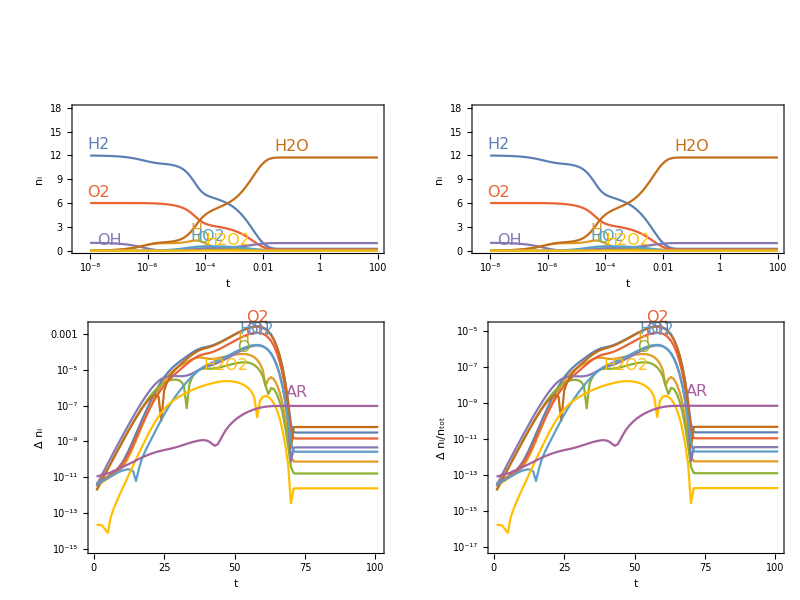

errors.pdf

```mathematica
num=6;
filebase="data/errors/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"};
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,dat[[2]]];
states1=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
concentrations1=Table[Transpose[{times,(Total/@(states1.concentrationnorms[[i]]))}],{i,1,ns}];
filebase="data/errors2/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
elements=dat[[3]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
concentrationnorms=Table[SparseArray[({#,#}&/@Range[dim])->(#[[i]]&/@multiindices)],{i,1,ns}];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,dat[[2]]];
states2=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
concentrations2=Table[Transpose[{times,(Total/@(states2.concentrationnorms[[i]]))}],{i,1,ns}];
p=Grid[{{ListLogLinearPlot[concentrations1,PlotRange->{0,3*num},ImageSize->350,ImagePadding->{{75,15},{75,75}},Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],Axes->False,Frame->True,FrameLabel->{{Subscript[n,i],None},{t,"Full state space"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]],ListLogLinearPlot[concentrations2,PlotRange->{0,3*num},ImageSize->350,ImagePadding->{{75,15},{75,75}},Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],Axes->False,Frame->True,FrameLabel->{{Subscript[n,i],None},{t,"Dimension reduced"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]},{ListLogPlot[Abs[(concentrations1[[All,All,2]]-concentrations2[[All,All,2]])],PlotRange->All,Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],ImageSize->350,ImagePadding->{{75,15},{75,15}},Axes->False,Frame->True,FrameLabel->{{Δ * Subscript[n,i],None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]],
ListLogPlot[Transpose[Transpose[Abs[(concentrations1[[All,All,2]]-concentrations2[[All,All,2]])]]/(Total[concentrations1[[All,All,2]]])],PlotRange->All,Joined->True,PlotLabels->Placed[Table[Style[species[[i]],ColorData[97,"ColorList"][[i]]],{i,1,ns}],Above],ImageSize->350,ImagePadding->{{75,15},{75,15}},Axes->False,Frame->True,FrameLabel->{{DisplayForm[RowBox[{Δ * Subscript[n,i],"/",Subscript[n,"tot"]}]],None},{t,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]}}]
Export["errors.pdf",p]
```

```mathematica
Monitor[Do[filebase="data/errors/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
ind=First@FirstPosition[multiindices,dat[[2]]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
thrs=10^-3;
vals=A["NonzeroValues"];
pos=A["NonzeroPositions"];
Do[If[A[[pos[[i,1]],pos[[i,2]]]]<thrs*A[[pos[[i,2]],pos[[i,1]]]],vals[[i]]=0],{i,1,Length[pos]}]
A2=SparseArray[#[[1]]->#[[2]]&/@Transpose[{pos,vals}]];

at1=AbsoluteTiming[{tvals,tvecs}=Eigensystem[Normal[Transpose[A2-SparseArray[Table[{i,i}->(Total/@A2)[[i]],{i,1,dim}],{dim,dim}]]]];];
at2=AbsoluteTiming[tinv=PseudoInverse[tvecs];];
tvals[[-1]]=0;
α=SparseArray[{ind->1},{dim}].tinv;
states2=Table[pos=Flatten[Position[tvals*t,u_/;Abs[u]<100]];(Exp[tvals[[pos]]*t]*α[[pos]]).tvecs[[pos]],{t,times}];
file=OpenWrite[filebase<>"tvals.dat",BinaryFormat->True];
BinaryWrite[file,tvals,"Complex64"];
Close[file];
file=OpenWrite[filebase<>"tvecs.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[tvecs],"Complex64"];
Close[file];
file=OpenWrite[filebase<>"tinv.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[tinv],"Complex64"];
Close[file];
file=OpenWrite[filebase<>"tstates.dat",BinaryFormat->True];
BinaryWrite[file,Re[Flatten[states2]],"Real64"];
Close[file];,{num,3,10,1}];,{at1,at2}]
```

```mathematica
vals=Table[filebase="data/errors/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
tstates=Partition[Import[filebase<>"tstates.dat","Real64"],dim];
{Table[{times[[i]],Norm[states[[i]]-tstates[[i]],Infinity]},{i,1,Length[times]}],Max[Abs[Re[states]-Re[tstates]]]},{num,3,10,1}];
ListLogLogPlot[vals[[All,1]],PlotRange->All,ImageSize->350,Axes->False,Frame->True,FrameLabel->{t,Abs[P-Subscript[P,unpruned]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],Joined->True,PlotLabels->Table[i,{i,3,10}]]
```

-Graphics-

```mathematica
Max[vals[[-1,1,All,2]]]
```

0.00795976

```mathematica
lists={};
stateses={};
Monitor[Do[
filebase="data/errors2/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim2,ns,runtime}=dat[[1,1;;3]];
times2=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices2=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
states2=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim2];

filebase="data/errors/"<>ToString[num];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime}=dat[[1,1;;3]];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
evals=BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]];
evecs=Partition[BinaryReadList[filebase<>"eigenvectors.npy","Complex128"][[9;;-1]],dim];
ind=FirstPosition[multiindices,dat[[2]]];
pos1=Sort[First@FirstPosition[multiindices2,#]&/@multiindices];
pos2=Complement[Range[dim2],pos1];

thrsmin=-1*10^6;
thrsmax=-1*10^8;
dthrs=-5*10^6;
e1=Total/@Abs[states2[[All,pos2]]];
states4=states2[[All,pos1]];
AppendTo[stateses,{states,states2[[All,pos1]],states2[[All,pos2]]}];
list=Table[
index=First@FirstPosition[evals,u_/;Re[u]>thrs];
evals3=evals[[index;;-1]];
evecs3=evecs[[index;;-1]];
evals3[[-1]]=0;
AbsoluteTiming[pinv=PseudoInverse[evecs3];];
AbsoluteTiming[α=SparseArray[{ind->1},{dim}].pinv;];
AbsoluteTiming[states3=Table[pos=Flatten[Position[evals3*t,u_/;Abs[u]<100]];(Exp[evals3[[pos]]*t]*α[[pos]]).evecs3[[pos]],{t,times}];];
{thrs,Max[Table[Total[Abs[states4[[n]]-states3[[n]]]]+e1[[n]],{n,1,Length[states]}]],Max[Table[Total[Abs[states[[n]]-states3[[n]]]],{n,1,Length[states]}]],Max[Norm[Flatten[states4-states3],Infinity],Norm[Flatten[e1],Infinity]],index,dim,dim2},{thrs,thrsmin,thrsmax,dthrs}];AppendTo[lists,list];,{num,3,8}],{num,thrs,N[(thrs-thrsmin)/(thrsmax-thrsmin)]}]
```

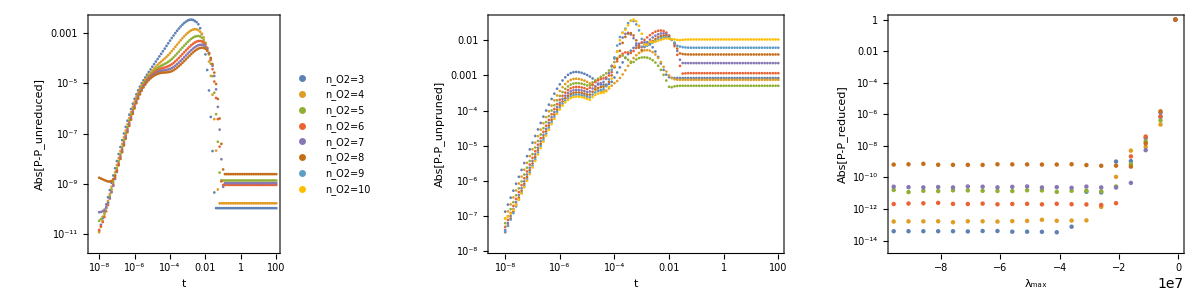

errors.pdf

```mathematica
p=Legended[Grid[{{ListLogLogPlot[Table[Table[{times[[n]],Total[Abs[stateses[[m,1,n]]-stateses[[m,2,n]]]]+Total[Abs[stateses[[m,3,n]]]]},{n,1,Length[states]}],{m,1,Length[stateses]}],PlotRange->All,ImageSize->350,Axes->False,Frame->True,FrameLabel->{t,Abs[P-Subscript[P,unreduced]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16]],ListLogLogPlot[vals[[All,1]],PlotRange->All,ImageSize->350,Axes->False,Frame->True,FrameLabel->{t,Abs[P-Subscript[P,unpruned]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],Joined->False],ListLogPlot[lists[[All,All,{1,3}]],Joined->False,PlotRange->All,ImageSize->350,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{Subscript[λ,max],Abs[P-Subscript[P,reduced]]}]}}],PointLegend[ColorData[97,"ColorList"][[1;;8]],Table[DisplayForm[RowBox[{Subscript[n,O2],"=",i}]],{i,3,10}]]]
Export["errors.pdf",p]
```

### example enumeration

```mathematica
filebase="data/example2";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
temp=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pres=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
states=Partition[Import[filebase<>"states.npy","Real64"][[17;;-1]],dim];
A=SparseArray[Join[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}]],{dim,dim}];
species={"H2","H","O","O2","OH","H2O","HO2","H2O2","AR"}
st=Transpose[{ToString[Total[species*#]]&/@multiindices,temp,pres}]
filebase="data/example1";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]];
multiindices1=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[dat[[2]]]];
inaccessible=Complement[multiindices1,multiindices]
Export["example.csv",Join[st,Transpose[{ToString[Total[species*#]]&/@inaccessible,ConstantArray[0,Length[inaccessible]],ConstantArray[0,Length[inaccessible]]}]]]
```

{H2,H,O,O2,OH,H2O,HO2,H2O2,AR}

{{20 AR + 2 H2 + O2,1000.,1.},{20 AR + H2 + 2 OH,754.911,0.754911},{20 AR + H2 + H2O + O,984.795,0.984795},{20 AR + H + H2O + OH,959.135,0.959135},{20 AR + 2 H2O,2472.97,2.36545},{20 AR + H + H2 + HO2,269.276,0.269276},{20 AR + H2 + H2O2,1404.04,1.34299},{20 AR + 2 H + H2O2,40.3128,0.0403128}}

{{0,2,0,0,2,0,0,0,20},{0,2,1,0,0,1,0,0,20},{0,3,0,0,0,0,1,0,20},{0,3,1,0,1,0,0,0,20},{0,4,0,1,0,0,0,0,20},{0,4,2,0,0,0,0,0,20},{1,1,1,0,1,0,0,0,20},{1,2,0,1,0,0,0,0,20},{1,2,2,0,0,0,0,0,20},{2,0,2,0,0,0,0,0,20}}

example.csv

```mathematica
ToString[Total[species*#]]&/@inaccessible
```

{20 AR + 2 H + 2 OH,20 AR + 2 H + H2O + O,20 AR + 3 H + HO2,20 AR + 3 H + O + OH,20 AR + 4 H + O2,20 AR + 4 H + 2 O,20 AR + H + H2 + O + OH,20 AR + 2 H + H2 + O2,20 AR + 2 H + H2 + 2 O,20 AR + 2 H2 + 2 O}

```mathematica
filebase="data/nodimred_old/9";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1,1;;3]];
evals=BinaryReadList[filebase<>"eigenvalues.npy","Complex128"][[9;;-1]];
Length[evals]
```

2000